```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

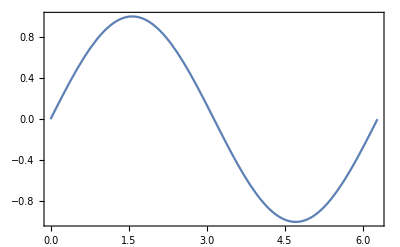

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
Plot[Sin[x],{x,0,2 Pi},Frame->True,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{"x","\\sin x"},BaseStyle->texStyle]
```

# plots with η = 1

### Exact

Exact solution via Laplace inverse transfotm

```mathematica
fse[s_,a_,η_]:=η(-ⅈ +ⅇ^(-(ⅈ s+a)) (s-ⅈ a)Gamma[0,-ⅈ (s-ⅈ a)])
c1[t_,a_,η_]:=ResourceFunction["NInverseLaplaceTransform"][1/(s+fse[s,a,η]),s,t]
ρ11[t_,a_,η_]:=Norm[c1[t,a,η]]^2
ρ11pts[t0_,tf_,step_,a_,η_]:=
Thread[{Table[i,{i,t0,tf,step}],Table[ρ11[i,a,η],{i,t0,tf,step}]}]
```

### Coarse Graining

The rate for the course graining for ohmic model

```mathematica
bww[t_,ω_,η_]:=η ⅇ^-ω((1-ω-I ω t)ExpIntegralEi[ω+I ω t]+(1-ω+I ω t)ExpIntegralEi[ω-I ω t]+2(ω-1)ExpIntegralEi[ω])+2η(1-Cos[ ω t])
γww[t_,ω_,η_]:=bww[t,ω,η]/t
FullSimplify[bww[t,ω,η]];
```

### TCL

#### TCL2

```mathematica
γTCL2[t_,a_,η_]:=2η((t Cos[a t]-Sin[a t])/(1+t^2)+a Exp[-a]Im[ExpIntegralEi[a( 1+I t)]])
ρTCL2[t_,a_,η_]:=Exp[-NIntegrate[γTCL2[u,a,η],{u,0,t}]]
```

#### TCL4

```mathematica
fad[u_,a_,η_]:=η ⅇ^(ⅈ a u)/(ⅈ u+1)^2
Zad[u_,u1_,a_,η_]:= η(ⅇ^(ⅈ a u)/(1+ⅈ u)-ⅇ^(ⅈ a (u-u1))/(1+ⅈ (u-u1))+a ⅇ^-a (ExpIntegralEi[a (1+ⅈ (u-u1))]-ExpIntegralEi[a (1+ⅈ u)]))
Int2[u_?NumberQ,u1_?NumberQ,a_?NumberQ,η_]:=NIntegrate[(fad[u-u2,a,η] Zad[u1,u2,a,η]+fad[u1-u2,a,η] Zad[u,u2,a,η]),{u2,0,u1},Method->{Automatic,"SymbolicProcessing"->0}];

γTCL4[u_?NumberQ,a_?NumberQ,η_]:=γTCL2[u,a,η]+2 Re[ⅈ NIntegrate[Int2[u,u1,a,η],{u1,0,u},Method->{Automatic,"SymbolicProcessing"->0}]];
ρTCL4[t_,a_,η_]:=Exp[-NIntegrate[γTCL4[u,a,η],{u,0,t}]]
ρTCL4faster[t_,a_,η_]:=Exp[-NIntegrate[γTCL4[u,a,η],{u,0,t},Method->{"LocalAdaptive","SymbolicProcessing"->0},PrecisionGoal->2]]
```

## Examples with a=1

1

{{0,1},{0.01,0.9999},{0.11,0.987985},{0.21,0.957009},{0.31,0.909029},{0.41,0.847054},{0.51,0.774669},{0.61,0.695656},{0.71,0.613671},{0.81,0.532015},{0.91,0.453479},{1.01,0.38028},{1.11,0.314042},{1.21,0.255819},{1.31,0.206155},{1.41,0.165145},{1.51,0.132519},{1.61,0.107718},{1.71,0.0899746},{1.81,0.078383},{1.91,0.071966},{2.01,0.0697297},{2.11,0.0707097},{2.21,0.0740066},{2.31,0.0788125},{2.41,0.0844281},{2.51,0.0902712},{2.61,0.0958792},{2.71,0.100905},{2.81,0.105111},{2.91,0.108353},{3.01,0.110571},{3.11,0.111775},{3.21,0.112027},{3.31,0.111428},{3.41,0.110106},{3.51,0.108203},{3.61,0.105865},{3.71,0.103233},{3.81,0.10044},{3.91,0.097601},{4.01,0.0948155},{4.11,0.092162},{4.21,0.0896998},{4.31,0.0874689},{4.41,0.0854925},{4.51,0.083778},{4.61,0.0823203},{4.71,0.0811041},{4.81,0.0801065},{4.91,0.0792995},{5.01,0.0786523},{5.11,0.0781332},{5.21,0.0777113},{5.31,0.0773578},{5.41,0.077047},{5.51,0.0767567},{5.61,0.0764688},{5.71,0.0761693},{5.81,0.0758481},{5.91,0.0754987},{6.01,0.0751179},{6.11,0.0747054},{6.21,0.0742629},{6.31,0.0737939},{6.41,0.0733031},{6.51,0.072796},{6.61,0.0722781},{6.71,0.0717552},{6.81,0.0712326},{6.91,0.070715},{7.01,0.0702065},{7.11,0.0697104},{7.21,0.0692292},{7.31,0.0687647},{7.41,0.0683177},{7.51,0.0678887},{7.61,0.0674773},{7.71,0.0670828},{7.81,0.0667043},{7.91,0.0663403},{8.01,0.0659895},{8.11,0.0656504},{8.21,0.0653214},{8.31,0.0650011},{8.41,0.0646883},{8.51,0.0643818},{8.61,0.0640806},{8.71,0.0637839},{8.81,0.0634912},{8.91,0.0632019},{9.01,0.0629158},{9.11,0.0626327},{9.21,0.0623526},{9.31,0.0620754},{9.41,0.0618012},{9.51,0.0615302},{9.61,0.0612625},{9.71,0.0609983},{9.81,0.0607377},{9.91,0.0604808},{10.1,0.0600034},{11.1,0.0577187},{12.1,0.0557479},{13.1,0.054008},{14.1,0.0524605},{15.1,0.0510734},{16.1,0.0498199},{17.1,0.0486798},{18.1,0.0476369},{19.1,0.0466782},{20.1,0.0457926},{21.1,0.0449714},{22.1,0.044207},{23.1,0.0434931},{24.1,0.0428242},{25.1,0.0421959},{26.1,0.041604},{27.1,0.0410452},{28.1,0.0405165},{29.1,0.0400152},{30.1,0.039539},{31.1,0.0390858},{32.1,0.0386539},{33.1,0.0382415},{34.1,0.0378472},{35.1,0.0374697},{36.1,0.0371079},{37.1,0.0367606},{38.1,0.0364269},{39.1,0.0361059},{100,0.0267224},{110,0.0259706},{120,0.0253103},{130,0.0247239},{140,0.0241981},{150,0.0237228},{160,0.0232903},{170,0.0228941},{180,0.0225295},{190,0.0221921},{200,0.0218787}}

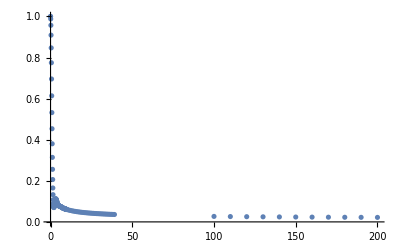

InterpolatingFunction[…]

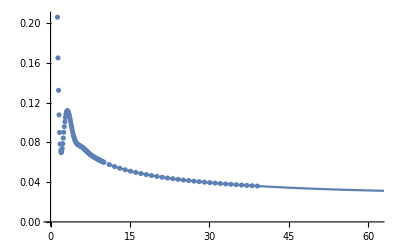

```mathematica
a=1
η=1;
T=200;
ρ11ptsList1=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,40,1,a,η],ρ11pts[100,200,10,a,η]]

ListPlot[{ρ11ptsList1},PlotRange->All]
ρ11pts1=Interpolation[ρ11ptsList1]
Show[{ListPlot[ρ11ptsList1],Plot[ρ11pts1[t],{t,0,T}]}]
```

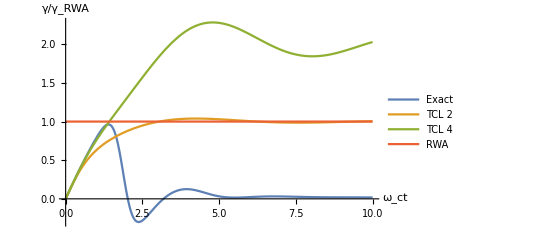

```mathematica
Plot[{(-ρ11pts1'[t]/ρ11pts1[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,10},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

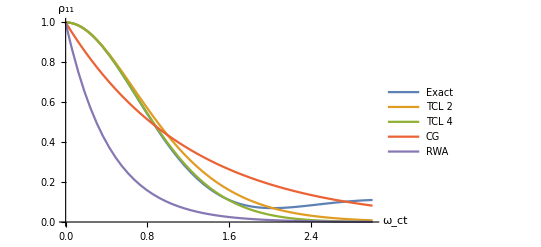

```mathematica
Plot[{ρ11pts1[t],ρTCL2[t,a,η],ρTCL4faster[t,a,η],Exp[-Re[γww[0.280982408523559,a,η]]t],Exp[-2π η a ⅇ^(- a)t]},{t,0,3},PlotLegends->{"Exact","TCL 2","TCL 4","CG","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

### Examples with a = 3

3

{{0,1},{0.01,0.9999},{0.11,0.987985},{0.21,0.957016},{0.31,0.909099},{0.41,0.847399},{0.51,0.775823},{0.61,0.698646},{0.71,0.620148},{0.81,0.544271},{0.91,0.474352},{1.01,0.412921},{1.11,0.361596},{1.21,0.321057},{1.31,0.291107},{1.41,0.270789},{1.51,0.258564},{1.61,0.25251},{1.71,0.250533},{1.81,0.250573},{1.91,0.250775},{2.01,0.249625},{2.11,0.246042},{2.21,0.239413},{2.31,0.229587},{2.41,0.216823},{2.51,0.201706},{2.61,0.185046},{2.71,0.167763},{2.81,0.150777},{2.91,0.134917},{3.01,0.12084},{3.11,0.108986},{3.21,0.0995566},{3.31,0.0925197},{3.41,0.0876395},{3.51,0.0845223},{3.61,0.0826743},{3.71,0.0815627},{3.81,0.0806738},{3.91,0.0795628},{4.01,0.0778906},{4.11,0.075446},{4.21,0.0721513},{4.31,0.0680541},{4.41,0.063306},{4.51,0.058134},{4.61,0.0528057},{4.71,0.0475953},{4.81,0.0427518},{4.91,0.0384742},{5.01,0.0348946},{5.11,0.0320698},{5.21,0.029983},{5.31,0.0285524},{5.41,0.0276466},{5.51,0.0271036},{5.61,0.026751},{5.71,0.026425},{5.81,0.0259873},{5.91,0.0253369},{6.01,0.0244162},{6.11,0.0232128},{6.21,0.0217553},{6.31,0.0201052},{6.41,0.0183466},{6.51,0.0165737},{6.61,0.014879},{6.71,0.0133429},{6.81,0.0120254},{6.91,0.0109616},{7.01,0.0101594},{7.11,0.00960168},{7.21,0.00925027},{7.31,0.00905202},{7.41,0.00894611},{7.51,0.00887146},{7.61,0.00877334},{7.71,0.00860871},{7.81,0.00834967},{7.91,0.00798495},{8.01,0.00751928},{8.11,0.00697113},{8.21,0.00636907},{8.31,0.0057474},{8.41,0.00514152},{8.51,0.00458372},{8.61,0.00409963},{8.71,0.00370587},{8.81,0.00340894},{8.91,0.00320534},{9.01,0.00308286},{9.11,0.00302272},{9.21,0.00300228},{9.31,0.00299789},{9.41,0.00298765},{9.51,0.00295367},{9.61,0.00288363},{9.71,0.00277164},{9.81,0.00261822},{9.91,0.00242957},{10.1,0.00201406},{12.1,0.000536404},{14.1,0.000132977},{16.1,0.0000340929},{18.1,0.0000118649},{20.1,5.90188×10^-6},{22.1,3.08785×10^-6},{24.1,1.38948×10^-6},{26.1,5.01084×10^-7},{28.1,1.4746×10^-7},{30.1,5.48134×10^-8},{32.1,4.81017×10^-8},{34.1,5.20643×10^-8},{36.1,4.8587×10^-8},{38.1,4.00419×10^-8}}

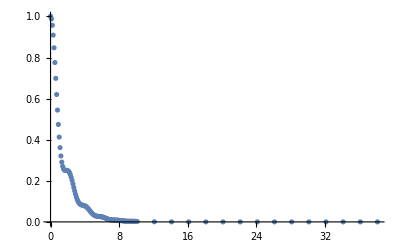

InterpolatingFunction[…]

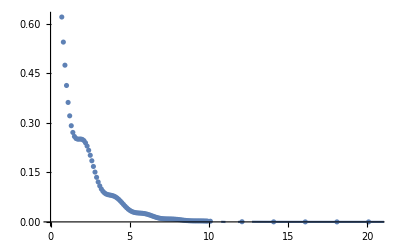

```mathematica
a=3
η=1;
T=200;
ρ11ptsList3=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,40,2,a,η]]
(*,ρ11pts[100,200,10,a,η]]*)

ListPlot[{ρ11ptsList3},PlotRange->All]
ρ11pts3=Interpolation[ρ11ptsList3]
Show[{ListPlot[ρ11ptsList3],Plot[ρ11pts3[t],{t,0,T}]}]
```

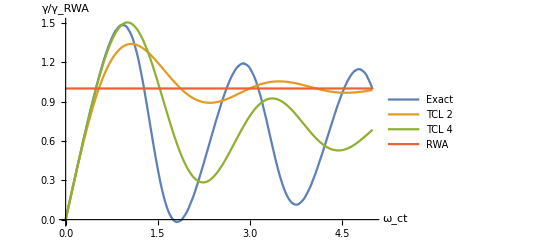

```mathematica
Plot[{(-ρ11pts3'[t]/ρ11pts3[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,5},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

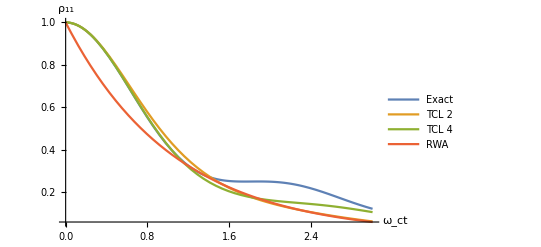

```mathematica
Plot[{ρ11pts3[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,3},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

### Examples with a = 4

4

{{0,1},{0.01,0.9999},{0.11,0.988021},{0.21,0.957488},{0.31,0.911266},{0.41,0.853719},{0.51,0.790047},{0.61,0.72563},{0.71,0.665391},{0.81,0.613259},{0.91,0.571788},{1.01,0.541989},{1.11,0.523367},{1.21,0.514151},{1.31,0.511665},{1.41,0.512792},{1.51,0.514433},{1.61,0.513933},{1.71,0.509386},{1.81,0.499815},{1.91,0.485191},{2.01,0.466316},{2.11,0.444605},{2.21,0.421793},{2.31,0.39963},{2.41,0.379613},{2.51,0.362779},{2.61,0.349593},{2.71,0.33994},{2.81,0.333206},{2.91,0.328428},{3.01,0.324485},{3.11,0.320296},{3.21,0.314987},{3.31,0.308008},{3.41,0.299193},{3.51,0.288741},{3.61,0.277146},{3.71,0.265084},{3.81,0.253283},{3.91,0.242393},{4.01,0.232885},{4.11,0.224989},{4.21,0.218676},{4.31,0.213689},{4.41,0.209606},{4.51,0.205925},{4.61,0.202156},{4.71,0.197905},{4.81,0.192927},{4.91,0.187157},{5.01,0.180702},{5.11,0.173804},{5.21,0.166791},{5.31,0.160007},{5.41,0.153752},{5.51,0.148233},{5.61,0.143536},{5.71,0.13962},{5.81,0.136336},{5.91,0.13346},{6.01,0.130737},{6.11,0.127931},{6.21,0.124859},{6.31,0.121424},{6.41,0.117618},{6.51,0.113521},{6.61,0.109274},{6.71,0.105054},{6.81,0.101033},{6.91,0.0973543},{7.01,0.094103},{7.11,0.0912986},{7.21,0.0888952},{7.31,0.0867944},{7.41,0.0848666},{7.51,0.082976},{7.61,0.0810048},{7.71,0.0788727},{7.81,0.0765474},{7.91,0.0740467},{8.01,0.0714309},{8.11,0.0687884},{8.21,0.0662174},{8.31,0.0638072},{8.41,0.0616224},{8.51,0.0596929},{8.61,0.0580108},{8.71,0.0565342},{8.81,0.0551971},{8.91,0.0539227},{9.01,0.0526376},{9.11,0.0512851},{9.21,0.0498332},{9.31,0.0482788},{9.41,0.0466461},{9.51,0.0449793},{9.61,0.0433338},{9.71,0.0417645},{9.81,0.0403159},{9.91,0.0390143},{10.1,0.0369463},{12.1,0.0205872},{14.1,0.0109079}}

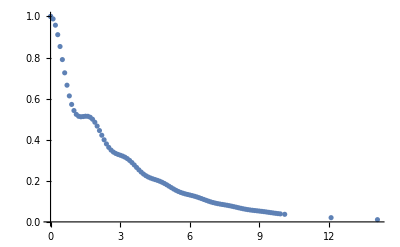

InterpolatingFunction[…]

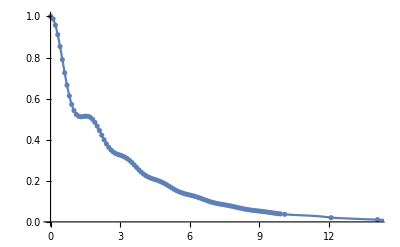

```mathematica
a=4
η=1;
T=200;
ρ11ptsList4=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,15,2,a,η]]
(*,ρ11pts[100,200,10,a,η]]*)

ListPlot[{ρ11ptsList4},PlotRange->All]
ρ11pts4=Interpolation[ρ11ptsList4]
Show[{ListPlot[ρ11ptsList4],Plot[ρ11pts4[t],{t,0,T}]}]
```

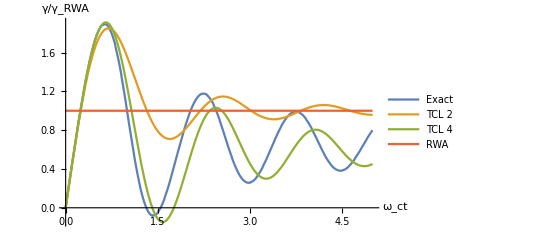

```mathematica
Plot[{(-ρ11pts4'[t]/ρ11pts4[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,5},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,3},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

$Aborted

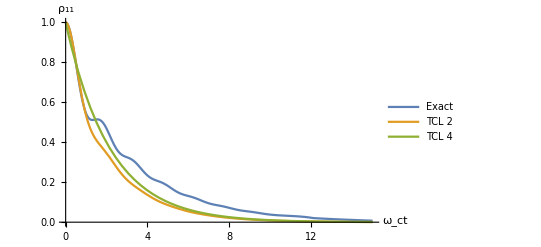

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,15},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

```mathematica
ρTCL4[4,a,η]
```

0.261603

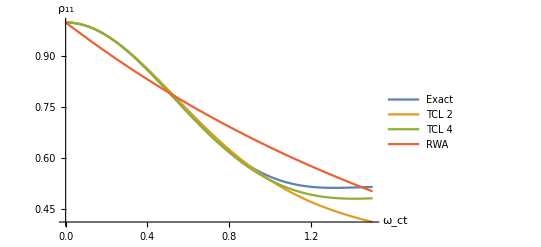

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,1.5},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

```mathematica
Table[{i,ρTCL4[i,a,η]},{i,0,4,0.1}]
```

$Aborted

```mathematica
ρTCL4pts=Join[ Table[{i, ρTCL4[i, a, η]}, {i, 0, 3, 0.1}], Table[{i, ρTCL4[i, a, η]}, {i, 3.1, 5, 0.5}]]
ρTCL4Easy=Interpolation[ρTCL4pts]
```

{{0.,1.},{0.1,0.990083},{0.2,0.961311},{0.3,0.916499},{0.4,0.859917},{0.5,0.796686},{0.6,0.732032},{0.7,0.670579},{0.8,0.615849},{0.9,0.570061},{1.,0.534205},{1.1,0.508266},{1.2,0.491475},{1.3,0.482515},{1.4,0.479659},{1.5,0.480869},{1.6,0.483926},{1.7,0.486614},{1.8,0.486977},{1.9,0.483579},{2.,0.475707},{2.1,0.463439},{2.2,0.447539},{2.3,0.429238},{2.4,0.409951},{2.5,0.391021},{2.6,0.373533},{2.7,0.358224},{2.8,0.345456},{2.9,0.335253},{3.,0.327351},{3.1,0.32127},{3.6,0.296095},{4.1,0.252117},{4.6,0.215428}}

InterpolatingFunction[…]

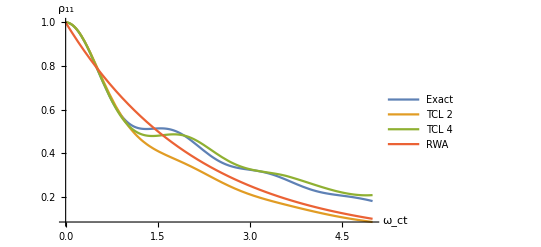

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],ρTCL4Easy[t],Exp[-2 π a η Exp[-a]t]},{t,0,5},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

with the legends on point

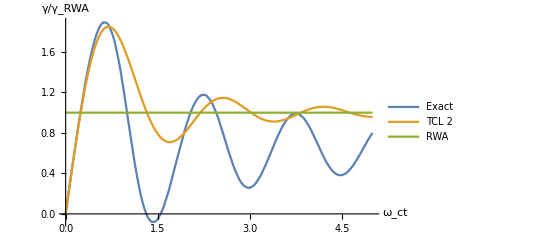

```mathematica
Plot[{(-ρ11pts4'[t]/ρ11pts4[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),1},{t,0,5},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","RWA"},{0.85,0.8}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

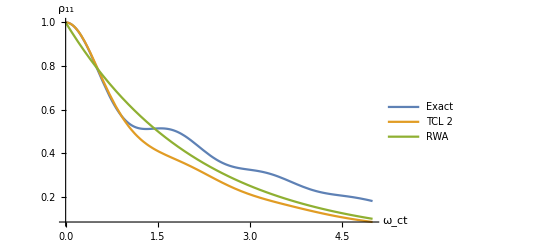

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,5},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","RWA"},{0.8,0.8}],AxesLabel->{"ω_ct","ρ_11"}]
```

Now we used Matlab to do the calculations, cause it is taking too much time

```mathematica
MATgamTCLa4=Import["/Users/jgarcian/Desktop/gamTCLa4.xlsx"]
```

{{{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.05,6.1,6.15,6.2,6.25,6.3,6.35,6.4,6.45,6.5,6.55,6.6,6.65,6.7,6.75,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.25,7.3,7.35,7.4,7.45,7.5,7.55,7.6,7.65,7.7,7.75,7.8,7.85,7.9,7.95,8.,8.05,8.1,8.15,8.2,8.25,8.3,8.35,8.4,8.45,8.5,8.55,8.6,8.65,8.7,8.75,8.8,8.85,8.9,8.95,9.,9.05,9.1,9.15,9.2,9.25,9.3,9.35,9.4,9.45,9.5,9.55,9.6,9.65,9.7,9.75,9.8,9.85,9.9,9.95,10.},{0.,0.0997503,0.198009,0.29332,0.384295,0.469645,0.54821,0.618983,0.681131,0.734011,0.777182,0.810407,0.83366,0.847115,0.85114,0.846286,0.833262,0.812922,0.786234,0.754258,0.718117,0.678966,0.637966,0.596253,0.554917,0.514969,0.477327,0.442794,0.412042,0.385604,0.363864,0.347059,0.335274,0.328452,0.326404,0.328816,0.335271,0.34526,0.358208,0.373488,0.390446,0.40842,0.42676,0.444848,0.462113,0.478047,0.492215,0.504268,0.513945,0.521079,0.525596,0.527511,0.526925,0.524017,0.519031,0.512267,0.504068,0.494807,0.484869,0.474645,0.464509,0.454817,0.445885,0.437991,0.431357,0.426153,0.422488,0.420412,0.419917,0.420938,0.42336,0.427025,0.431737,0.437271,0.443386,0.44983,0.45635,0.462705,0.468666,0.474035,0.478639,0.482343,0.485051,0.486707,0.487296,0.486843,0.485409,0.48309,0.480011,0.476317,0.472173,0.467753,0.463232,0.458786,0.454578,0.450756,0.44745,0.444763,0.442774,0.441531,0.441051,0.441326,0.442315,0.443957,0.446163,0.448831,0.451843,0.455071,0.458386,0.461658,0.464764,0.467593,0.470044,0.472039,0.473516,0.474435,0.474781,0.474559,0.473796,0.472538,0.47085,0.46881,0.466507,0.464038,0.461502,0.459,0.456625,0.454466,0.452599,0.451087,0.449978,0.449301,0.449072,0.449285,0.449919,0.450938,0.452292,0.453919,0.455748,0.457704,0.459706,0.461678,0.463542,0.465231,0.466683,0.467849,0.468691,0.469185,0.469321,0.469104,0.468551,0.467692,0.466568,0.465229,0.463734,0.462143,0.460521,0.458932,0.457437,0.456091,0.454943,0.454032,0.453389,0.453032,0.452968,0.453193,0.45369,0.454435,0.455393,0.45652,0.45777,0.459092,0.460431,0.461735,0.462955,0.464044,0.464964,0.465682,0.466174,0.466426,0.466434,0.466203,0.465746,0.465087,0.464256,0.463288,0.462225,0.461109,0.459986,0.4589,0.457891,0.456999,0.456256,0.455687,0.455311,0.455139,0.455174,0.45541,0.455834,0.456426,0.457159},{0.,0.099833,0.198657,0.295429,0.389042,0.47831,0.561958,0.638644,0.706982,0.765595,0.813175,0.848554,0.870778,0.879181,0.873447,0.853662,0.820345,0.774451,0.717366,0.650855,0.577012,0.498174,0.416829,0.33552,0.256735,0.182816,0.115866,0.0576744,0.00966212,-0.0271592,-0.0522045,-0.0653147,-0.0667378,-0.0570963,-0.037341,-0.00869769,0.0273926,0.0693349,0.115442,0.163992,0.213284,0.261691,0.307696,0.349938,0.387238,0.418629,0.443371,0.460966,0.471164,0.473963,0.4696,0.458541,0.441456,0.419196,0.392756,0.363242,0.331831,0.299721,0.268095,0.238076,0.210687,0.186819,0.1672,0.152374,0.142688,0.138286,0.139113,0.144922,0.155292,0.169651,0.187303,0.207459,0.22927,0.251856,0.274347,0.295907,0.315766,0.333244,0.347773,0.358913,0.366364,0.369974,0.369734,0.365783,0.35839,0.347948,0.334952,0.319976,0.303656,0.28666,0.26966,0.253313,0.238229,0.224955,0.213952,0.205579,0.200084,0.197597,0.198129,0.201572,0.207709,0.216225,0.226722,0.238736,0.251757,0.265252,0.278681,0.291523,0.303295,0.313564,0.321969,0.32823,0.332154,0.333646,0.332707,0.32943,0.323999,0.316676,0.307791,0.297729,0.286911,0.275778,0.264776,0.254335,0.244855,0.236688,0.23013,0.225404,0.222658,0.221961,0.223296,0.226569,0.23161,0.238185,0.246002,0.254728,0.263999,0.273439,0.282671,0.291334,0.299098,0.305673,0.310821,0.314366,0.316196,0.316272,0.31462,0.311337,0.306581,0.300567,0.293554,0.285836,0.277732,0.269568,0.261671,0.254348,0.247881,0.242513,0.238439,0.235799,0.234677,0.235092,0.237003,0.240311,0.244862,0.250457,0.256857,0.263795,0.270988,0.278146,0.284985,0.291239,0.296668,0.301068,0.304281,0.306195,0.306754,0.305953,0.303845,0.300531,0.296158,0.290916,0.285025,0.278726,0.272277,0.265935,0.259952,0.254559,0.249966,0.246343,0.243823,0.242491,0.242385,0.243495,0.24576,0.249076,0.253297,0.258245,0.263713,0.269477,0.275305}}}

(0. | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9 | 0.95 | 1. | 1.05 | 1.1 | 1.15 | 1.2 | 1.25 | 1.3 | 1.35 | 1.4 | 1.45 | 1.5 | 1.55 | 1.6 | 1.65 | 1.7 | 1.75 | 1.8 | 1.85 | 1.9 | 1.95 | 2. | 2.05 | 2.1 | 2.15 | 2.2 | 2.25 | 2.3 | 2.35 | 2.4 | 2.45 | 2.5 | 2.55 | 2.6 | 2.65 | 2.7 | 2.75 | 2.8 | 2.85 | 2.9 | 2.95 | 3. | 3.05 | 3.1 | 3.15 | 3.2 | 3.25 | 3.3 | 3.35 | 3.4 | 3.45 | 3.5 | 3.55 | 3.6 | 3.65 | 3.7 | 3.75 | 3.8 | 3.85 | 3.9 | 3.95 | 4. | 4.05 | 4.1 | 4.15 | 4.2 | 4.25 | 4.3 | 4.35 | 4.4 | 4.45 | 4.5 | 4.55 | 4.6 | 4.65 | 4.7 | 4.75 | 4.8 | 4.85 | 4.9 | 4.95 | 5. | 5.05 | 5.1 | 5.15 | 5.2 | 5.25 | 5.3 | 5.35 | 5.4 | 5.45 | 5.5 | 5.55 | 5.6 | 5.65 | 5.7 | 5.75 | 5.8 | 5.85 | 5.9 | 5.95 | 6. | 6.05 | 6.1 | 6.15 | 6.2 | 6.25 | 6.3 | 6.35 | 6.4 | 6.45 | 6.5 | 6.55 | 6.6 | 6.65 | 6.7 | 6.75 | 6.8 | 6.85 | 6.9 | 6.95 | 7. | 7.05 | 7.1 | 7.15 | 7.2 | 7.25 | 7.3 | 7.35 | 7.4 | 7.45 | 7.5 | 7.55 | 7.6 | 7.65 | 7.7 | 7.75 | 7.8 | 7.85 | 7.9 | 7.95 | 8. | 8.05 | 8.1 | 8.15 | 8.2 | 8.25 | 8.3 | 8.35 | 8.4 | 8.45 | 8.5 | 8.55 | 8.6 | 8.65 | 8.7 | 8.75 | 8.8 | 8.85 | 8.9 | 8.95 | 9. | 9.05 | 9.1 | 9.15 | 9.2 | 9.25 | 9.3 | 9.35 | 9.4 | 9.45 | 9.5 | 9.55 | 9.6 | 9.65 | 9.7 | 9.75 | 9.8 | 9.85 | 9.9 | 9.95 | 10.
0. | 0.0997503 | 0.198009 | 0.29332 | 0.384295 | 0.469645 | 0.54821 | 0.618983 | 0.681131 | 0.734011 | 0.777182 | 0.810407 | 0.83366 | 0.847115 | 0.85114 | 0.846286 | 0.833262 | 0.812922 | 0.786234 | 0.754258 | 0.718117 | 0.678966 | 0.637966 | 0.596253 | 0.554917 | 0.514969 | 0.477327 | 0.442794 | 0.412042 | 0.385604 | 0.363864 | 0.347059 | 0.335274 | 0.328452 | 0.326404 | 0.328816 | 0.335271 | 0.34526 | 0.358208 | 0.373488 | 0.390446 | 0.40842 | 0.42676 | 0.444848 | 0.462113 | 0.478047 | 0.492215 | 0.504268 | 0.513945 | 0.521079 | 0.525596 | 0.527511 | 0.526925 | 0.524017 | 0.519031 | 0.512267 | 0.504068 | 0.494807 | 0.484869 | 0.474645 | 0.464509 | 0.454817 | 0.445885 | 0.437991 | 0.431357 | 0.426153 | 0.422488 | 0.420412 | 0.419917 | 0.420938 | 0.42336 | 0.427025 | 0.431737 | 0.437271 | 0.443386 | 0.44983 | 0.45635 | 0.462705 | 0.468666 | 0.474035 | 0.478639 | 0.482343 | 0.485051 | 0.486707 | 0.487296 | 0.486843 | 0.485409 | 0.48309 | 0.480011 | 0.476317 | 0.472173 | 0.467753 | 0.463232 | 0.458786 | 0.454578 | 0.450756 | 0.44745 | 0.444763 | 0.442774 | 0.441531 | 0.441051 | 0.441326 | 0.442315 | 0.443957 | 0.446163 | 0.448831 | 0.451843 | 0.455071 | 0.458386 | 0.461658 | 0.464764 | 0.467593 | 0.470044 | 0.472039 | 0.473516 | 0.474435 | 0.474781 | 0.474559 | 0.473796 | 0.472538 | 0.47085 | 0.46881 | 0.466507 | 0.464038 | 0.461502 | 0.459 | 0.456625 | 0.454466 | 0.452599 | 0.451087 | 0.449978 | 0.449301 | 0.449072 | 0.449285 | 0.449919 | 0.450938 | 0.452292 | 0.453919 | 0.455748 | 0.457704 | 0.459706 | 0.461678 | 0.463542 | 0.465231 | 0.466683 | 0.467849 | 0.468691 | 0.469185 | 0.469321 | 0.469104 | 0.468551 | 0.467692 | 0.466568 | 0.465229 | 0.463734 | 0.462143 | 0.460521 | 0.458932 | 0.457437 | 0.456091 | 0.454943 | 0.454032 | 0.453389 | 0.453032 | 0.452968 | 0.453193 | 0.45369 | 0.454435 | 0.455393 | 0.45652 | 0.45777 | 0.459092 | 0.460431 | 0.461735 | 0.462955 | 0.464044 | 0.464964 | 0.465682 | 0.466174 | 0.466426 | 0.466434 | 0.466203 | 0.465746 | 0.465087 | 0.464256 | 0.463288 | 0.462225 | 0.461109 | 0.459986 | 0.4589 | 0.457891 | 0.456999 | 0.456256 | 0.455687 | 0.455311 | 0.455139 | 0.455174 | 0.45541 | 0.455834 | 0.456426 | 0.457159)

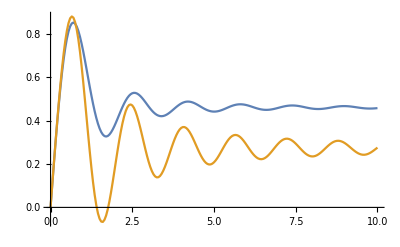

```mathematica
MATgamTCLa4={{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.05,6.1,6.15,6.2,6.25,6.3,6.35,6.4,6.45,6.5,6.55,6.6,6.65,6.7,6.75,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.25,7.3,7.35,7.4,7.45,7.5,7.55,7.6,7.65,7.7,7.75,7.8,7.85,7.9,7.95,8.,8.05,8.1,8.15,8.2,8.25,8.3,8.35,8.4,8.45,8.5,8.55,8.6,8.65,8.7,8.75,8.8,8.85,8.9,8.95,9.,9.05,9.1,9.15,9.2,9.25,9.3,9.35,9.4,9.45,9.5,9.55,9.6,9.65,9.7,9.75,9.8,9.85,9.9,9.95,10.},{0.,0.0997502914535423,0.198009306117987,0.293320411817143,0.384295215430714,0.469645113669054,0.548209911441939,0.618982757418994,0.681130801990203,0.734011141607348,0.777181765943408,0.810407366064837,0.833659992446534,0.847114672825763,0.851140213532124,0.846285515081106,0.833261833123706,0.81292150765143,0.786233764135797,0.754258257153659,0.718117077259223,0.67896597313921,0.637965551866044,0.596253209601558,0.554916513498131,0.514968703700385,0.477326913905911,0.442793622172474,0.412041743362218,0.385603663999459,0.363864402882328,0.347058960186495,0.335273797727248,0.328452277120764,0.326403774229926,0.328816090622259,0.335270698546362,0.345260287421081,0.358208028772019,0.373487944113001,0.390445747026425,0.408419536611124,0.426759743911139,0.44484777472342,0.462112849602991,0.47804661278679,0.49221516361561,0.504268254035319,0.513945490901332,0.521079479000531,0.525595936857817,0.527510909532975,0.526925287959867,0.524016920440958,0.519030666550469,0.512266795201747,0.504068165745823,0.494806652928772,0.484869283092566,0.474644540407179,0.464509278903036,0.454816639811669,0.445885325795542,0.437990525968433,0.431356720353911,0.426152521966577,0.422487641498714,0.420411986143948,0.419916832817195,0.420937949222934,0.423360475954612,0.427025330872688,0.431736854873897,0.437271386926216,0.443386436602558,0.449830114591392,0.456350485675773,0.462704523941673,0.468666375624297,0.474034669823575,0.478638659837164,0.482343026372558,0.48505122655614,0.486707327515969,0.487296318418234,0.486842948275499,0.485409186822657,0.483090450650904,0.480010775201634,0.476317144017749,0.472173208993948,0.467752648743634,0.463232416419586,0.458786123525478,0.454577792884827,0.450756192729532,0.447449935822632,0.444763493842188,0.442774239292556,0.441530586454519,0.441051260872012,0.441325685136286,0.442315428750312,0.44395663301415,0.446163289392039,0.448831222739745,0.451842609899599,0.455070850078532,0.458385596420242,0.46165775831185,0.464764291015789,0.467592602733236,0.470044428509876,0.472039044620921,0.473515725199004,0.474435373760993,0.474781294743843,0.474559102947062,0.473795800692966,0.472538082412677,0.47084995320689,0.468809770816125,0.466506838634146,0.464037690370005,0.461502214373728,0.458999767365858,0.456625423441408,0.454466495047007,0.45259944863644,0.451087319539578,0.449977709015759,0.449301422392864,0.449071781575614,0.449284619031977,0.449918934621644,0.450938172261289,0.45229205129943,0.453918868365466,0.455748169998822,0.45770368503954,0.459706398890009,0.461677649484506,0.463542127099345,0.465230666802932,0.466682733024682,0.467848509916267,0.468690528270008,0.469184779036043,0.469321284165513,0.469104116790455,0.468550883817784,0.467691704077246,0.466567733489926,0.46522930466523,0.463733761345115,0.462143077772215,0.460521359076641,0.458932321011183,0.457436845818886,0.456090705835207,0.454942537887812,0.454032140059675,0.453389148427476,0.453032135560967,0.452968155511798,0.453192742406376,0.453690352267551,0.454435220985342,0.455392596055167,0.4565202863539,0.457770463294916,0.459091638556631,0.46043073846533,0.461735193162185,0.462954959903483,0.464044404118695,0.464963968955761,0.465681573646668,0.466173692710394,0.46642608128552,0.466434126211365,0.46620281728542,0.465746347840417,0.465087367845639,0.464255925619736,0.463288145477099,0.462224697819795,0.461109125021448,0.459986090713035,0.458899621661348,0.457891410320819,0.456999242434356,0.456255607951305,0.455686545302114,0.455310759076456,0.455139039812363,0.455174002379692,0.455410146818566,0.455834232965127,0.456425948242667,0.457158837065153},{0.,0.0998330324016636,0.198657146796689,0.295429084478275,0.389042478417715,0.478309673597197,0.56195808556818,0.638643575974703,0.706981584139258,0.765594911794148,0.813175290550854,0.848554339188463,0.870778386950492,0.879181007647519,0.873447035928236,0.853662325454334,0.820344508852656,0.774451433578517,0.71736564191781,0.650855080608415,0.577012002872397,0.49817360944585,0.416829235760769,0.335519735254961,0.256735081852307,0.182816111207247,0.11586577693978,0.0576743886513444,0.00966212465419319,-0.0271592081444603,-0.0522045404732794,-0.0653146642236607,-0.066737820238584,-0.0570962829588885,-0.0373410125544607,-0.00869768950041183,0.0273925801766168,0.0693348526200056,0.115441605649684,0.163991558141203,0.213284472548755,0.261690865313532,0.307695972352615,0.349937632808337,0.387237955206836,0.418628725158347,0.443370525988452,0.46096550589922,0.471163673973302,0.473962577414338,0.46960023215621,0.45854126644944,0.441456398061356,0.419195593555788,0.392755534782563,0.363242316760168,0.331830591330073,0.299720620361194,0.268094882262947,0.238075964219287,0.210687457127908,0.186819448331564,0.16719998678229,0.152373593259248,0.142687528486701,0.138286142297694,0.139113236116693,0.144922005735749,0.155291813908141,0.169650788752031,0.187303063348041,0.207459366185683,0.229269636990073,0.251856368860498,0.274347453473799,0.295907418108076,0.315766078770946,0.333243782056985,0.347772561585595,0.358912688132181,0.366364243836564,0.369973500266766,0.369734028921218,0.365782622360477,0.358390255081836,0.347948464365512,0.334951679473623,0.319976167579442,0.303656389801166,0.286659662930264,0.269660094083762,0.253312789762886,0.238229332774687,0.224955467927535,0.213951841196045,0.205578501198282,0.20008370328724,0.197597364617027,0.198129314012628,0.201572274740417,0.207709322355216,0.216225383457702,0.226722192286284,0.238736006099792,0.251757300293489,0.26525162075132,0.278680762623338,0.291523468483937,0.303294890574588,0.313564136944386,0.321969315086667,0.32822959470669,0.332153929559539,0.333646203352972,0.332706693375175,0.329429874841363,0.323998716016748,0.316675735856448,0.307791208824808,0.297729002069309,0.286910614429113,0.275778051129127,0.264776209092553,0.254335462952719,0.244855129447076,0.236688447621501,0.230129645316922,0.225403571413122,0.222658262331396,0.221960685585888,0.223295768792193,0.226568685979461,0.231610240775165,0.238185064061141,0.246002237247032,0.254727865500593,0.263999060993875,0.273438756052672,0.28267075037427,0.291334404443561,0.2990984212611,0.305673208144615,0.310821376854125,0.314366020516006,0.316196496542465,0.316271542679333,0.314619655197681,0.311336760834512,0.306581314180315,0.300567046643429,0.293553678798831,0.285835981885003,0.277731633701986,0.269568356789918,0.26167085063029,0.25434803346062,0.247881092661452,0.242512805982741,0.238438540478791,0.235799264186974,0.234676820415279,0.235091619774868,0.237002805055414,0.240310843171677,0.244862401160038,0.250457273746698,0.256857052019666,0.263795159215552,0.27098783278899,0.278145603126721,0.284984809011111,0.291238697942759,0.296667684703975,0.301068382493437,0.304281075522493,0.306195367715388,0.306753816431867,0.305953440108645,0.303845071493859,0.300530610809075,0.296158312841411,0.290916315869229,0.285024685847456,0.278726304048512,0.272276968317721,0.265935105612554,0.259951505406834,0.254559479287879,0.24996583173215,0.246342991365872,0.2438226024278,0.242490814711072,0.24238543957745,0.243495062746169,0.245760124774288,0.249075900887515,0.253297236444437,0.258244825941597,0.263712764826361,0.269477056708074,0.275304725485969}};
{MATgamTCLa4[[1]],MATgamTCLa4[[2]]}//MatrixForm
γ2a4MAT=Transpose[{MATgamTCLa4[[1]],MATgamTCLa4[[2]]}];
γ4a4MAT=Transpose[{MATgamTCLa4[[1]],MATgamTCLa4[[3]]}];
ListLinePlot[{γ2a4MAT,γ4a4MAT}]
```

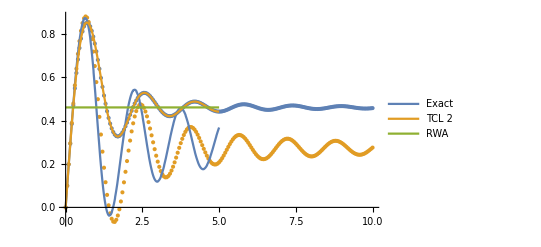

```mathematica
Show[{ListPlot[{γ2a4MAT,γ4a4MAT}], Plot[{(-ρ11pts4'[t]/ρ11pts4[t]),γTCL2[t,a,η],2 π a η Exp[-a]},{t,0,5},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","RWA"},{0.85,0.8}],AxesLabel->{"ω_ct","γ/γ_RWA"}]}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

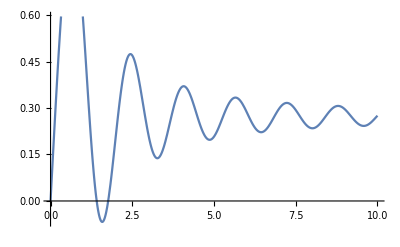

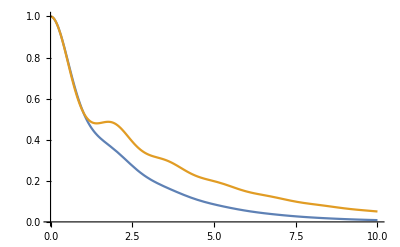

```mathematica
Clear[γ2a4f,ρTCL4MATa4]
γ2a4f=Interpolation[γ2a4MAT]
γ4a4f=Interpolation[γ4a4MAT]
Plot[γ4a4f[t],{t,0,10}]
ρTCL2MATa4[t_]:=Exp[-NIntegrate[γ2a4f[u],{u,0,t}]]
ρTCL4MATa4[t_]:=Exp[-NIntegrate[γ4a4f[u],{u,0,t}]]
Plot[{ρTCL2MATa4[t],ρTCL4MATa4[t]},{t,0,10}]
```

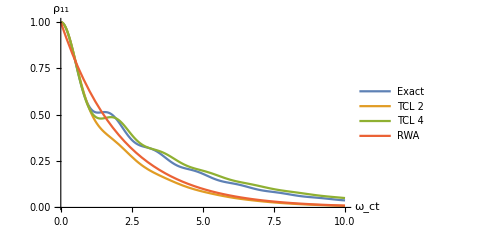

```mathematica
Plot[{ρ11pts4[t],ρTCL2[t,a,η],ρTCL4MATa4[t],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

```mathematica
a
```

1

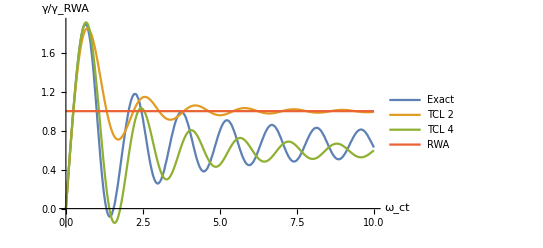

```mathematica
Plot[{(-ρ11pts4'[t]/ρ11pts4[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γ4a4f[t]/(2 π a η Exp[-a]),1},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.8}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

```mathematica
a
```

4

### Now with a=1

1

InterpolatingFunction[…]

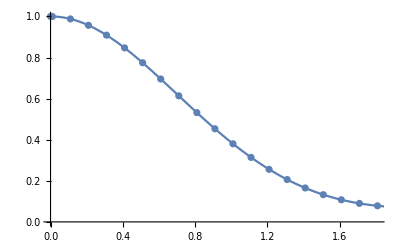

```mathematica
a=1
η=1;
T=200;
ρ11ptsList1={{0,1},{0.01,0.9999000058330249},{0.11,0.987984863617373},{0.21000000000000002,0.9570087207806984},{0.31000000000000005,0.9090286431878067},{0.41000000000000003,0.8470538215606391},{0.51,0.774669084353378},{0.6100000000000001,0.6956558326412349},{0.7100000000000001,0.6136714019723728},{0.81,0.5320146213203305},{0.91,0.45347893886644686},{1.01,0.3802801793830833},{1.11,0.314041503438304},{1.2100000000000002,0.2558190494779131},{1.31,0.20615462656616163},{1.4100000000000001,0.16514487525122945},{1.51,0.13251887266943893},{1.61,0.10771814624960846},{1.7100000000000002,0.08997459427531256},{1.81,0.07838302684531478},{1.9100000000000001,0.0719660367506394},{2.01,0.06972974525826448},{2.11,0.07070967271350874},{2.21,0.07400657188763038},{2.31,0.0788125394983188},{2.41,0.08442809289366404},{2.51,0.09027117001562353},{2.61,0.09587918892458686},{2.71,0.10090539791493576},{2.81,0.10511076978810605},{2.91,0.10835265643544163},{3.01,0.11057133518399972},{3.11,0.11177545884205675},{3.21,0.11202727880646532},{3.3099999999999996,0.11142835561431827},{3.4099999999999997,0.11010631320348448},{3.51,0.10820303960289747},{3.61,0.10586459389438285},{3.71,0.10323295156033202},{3.8099999999999996,0.1004396107279278},{3.9099999999999997,0.09760099194022909},{4.01,0.09481549433248483},{4.109999999999999,0.09216202088068733},{4.21,0.08969975334727419},{4.31,0.08746894172854006},{4.41,0.08549247108167059},{4.51,0.08377797804496091},{4.609999999999999,0.08232030758190845},{4.71,0.08110412497607947},{4.81,0.08010652655562861},{4.91,0.07929952296367047},{5.01,0.07865229924432618},{5.109999999999999,0.0781331851421399},{5.21,0.07771129570536546},{5.3100000000000005,0.07735782575407132},{5.41,0.07704700153317778},{5.51,0.07675670869481807},{5.609999999999999,0.07646882764623439},{5.71,0.07616931544482854},{5.8100000000000005,0.0758480781475605},{5.91,0.07549867925312824},{6.01,0.07511792909825302},{6.109999999999999,0.07470539729629287},{6.21,0.07426288604708237},{6.3100000000000005,0.07379389688507654},{6.41,0.0733031176084279},{6.51,0.07279595012807204},{6.609999999999999,0.07227809411296468},{6.71,0.071755195838115},{6.8100000000000005,0.07123256675254926},{6.91,0.07071497209872012},{7.01,0.07020648650032342},{7.11,0.06971041080988738},{7.21,0.06922924264788978},{7.31,0.06876469191642802},{7.41,0.0683177320540356},{7.51,0.06788867782015537},{7.61,0.06747728085607904},{7.71,0.06708283506019486},{7.8100000000000005,0.06670428483906221},{7.91,0.06634033045971571},{8.01,0.06598952595086298},{8.11,0.06565036621198099},{8.21,0.0653213611339004},{8.31,0.06500109557009305},{8.41,0.06468827489541183},{8.51,0.06438175663137456},{8.61,0.06408056919773494},{8.71,0.06378391927146443},{8.81,0.06349118950596275},{8.91,0.06320192850024904},{9.01,0.06291583492865459},{9.11,0.06263273766680157},{9.21,0.06235257360079518},{9.31,0.06207536460451094},{9.41,0.06180119493420617},{9.51,0.06153019003796205},{9.61,0.061262497524714465},{9.71,0.06099827079614893},{9.81,0.06073765562398662},{9.91,0.06048077976188994},{10.1,0.06000335962465749},{11.1,0.05771870107401328},{12.1,0.0557478982750559},{13.1,0.054007964605100704},{14.1,0.05246047132310152},{15.1,0.051073406569436826},{16.1,0.0498198638582816},{17.1,0.048679768053364735},{18.1,0.047636942367289055},{19.1,0.046678162713638},{20.1,0.045792636299371706},{21.1,0.044971411761669716},{22.1,0.04420699229399669},{23.1,0.04349305265784208},{24.1,0.0428242119400703},{25.1,0.04219585971694694},{26.1,0.04160402026515241},{27.1,0.04104524444832685},{28.1,0.04051652335252977},{29.1,0.040015218637835574},{30.1,0.03953900586667458},{31.1,0.03908582807225866},{32.1,0.038653857449839076},{33.1,0.0382414635419024},{34.1,0.037847186657414766},{35.1,0.03746971553766899},{36.1,0.03710786848995094},{37.1,0.036760577370592414},{38.1,0.03642687392269613},{39.1,0.03610587807028248},{100,0.026722365539476742},{110,0.025970593386224726},{120,0.02531032866483869},{130,0.024723895866662605},{140,0.024198095836914207},{150,0.02372284135281727},{160,0.023290269715942422},{170,0.022894146829567204},{180,0.022529455850985113},{190,0.02219210637149433},{200,0.0218787244417358}};
ρ11a1=Interpolation[ρ11ptsList1]
Show[{ListPlot[ρ11ptsList1[[1;;20]]],Plot[ρ11a1[t],{t,0,2}]}]
```

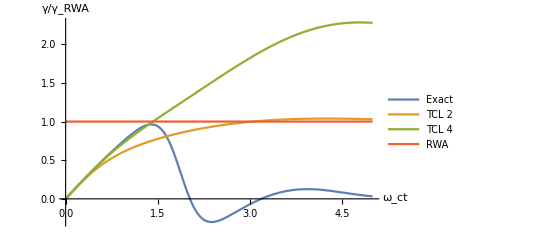

```mathematica
Plot[{(-ρ11a1'[t]/ρ11a1[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,5},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

```mathematica
MATgamTCLa1=Import["/Users/jgarcian/Desktop/gamTCLa1.xlsx"][[1]]
```

{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.},{0.,0.199009,0.392272,0.574977,0.743853,0.897317,1.03524,1.1585,1.26855,1.36706,1.45565,1.53582,1.60881,1.67571,1.73735,1.79443,1.84749,1.89695,1.94315,1.98636,2.02678,2.06458,2.09989,2.13284,2.1635,2.19196,2.2183,2.24258,2.26485,2.28519,2.30364,2.32028,2.33515,2.34832,2.35985,2.36982,2.37829,2.38532,2.39099,2.39538,2.39855,2.40059,2.40158,2.40158,2.40069,2.39897,2.39652,2.3934,2.38969,2.38547,2.38081,2.37579,2.37047,2.36493,2.35922,2.35342,2.34757,2.34174,2.33598,2.33033,2.32483,2.31954,2.31448,2.30969,2.3052,2.30102,2.29719,2.29371,2.2906,2.28786,2.28551,2.28355,2.28196,2.28075,2.27991,2.27942,2.27928,2.27947,2.27997,2.28076,2.28181,2.28311,2.28464,2.28636,2.28825,2.2903,2.29246,2.29471,2.29703,2.2994,2.30179,2.30417,2.30653,2.30884,2.31108,2.31323,2.31528,2.31721,2.319,2.32065,2.32215},{0.,0.199668,0.397361,0.591214,0.779591,0.961214,1.13525,1.30136,1.45964,1.61056,1.75486,1.89343,2.02724,2.15725,2.28434,2.40932,2.53287,2.65554,2.77776,2.8998,3.02183,3.14391,3.26598,3.38788,3.50939,3.6302,3.74996,3.86824,3.98461,4.0986,4.20972,4.31748,4.42139,4.52098,4.61578,4.70538,4.78936,4.86738,4.93911,5.00428,5.06269,5.11414,5.15854,5.19583,5.226,5.2491,5.26524,5.27457,5.27729,5.27367,5.26399,5.24859,5.22785,5.20216,5.17196,5.13769,5.09984,5.05889,5.01533,4.96967,4.9224,4.87403,4.82504,4.77591,4.7271,4.67905,4.63219,4.5869,4.54356,4.5025,4.46404,4.42844,4.39594,4.36675,4.34103,4.31892,4.3005,4.28585,4.27497,4.26787,4.26449,4.26475,4.26856,4.27577,4.28621,4.29971,4.31604,4.33497,4.35626,4.37963,4.40482,4.43153,4.45946,4.48833,4.51782,4.54765,4.5775,4.60711,4.63617,4.66444,4.69164}}

(0. | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1. | 1.1 | 1.2 | 1.3 | 1.4 | 1.5 | 1.6 | 1.7 | 1.8 | 1.9 | 2. | 2.1 | 2.2 | 2.3 | 2.4 | 2.5 | 2.6 | 2.7 | 2.8 | 2.9 | 3. | 3.1 | 3.2 | 3.3 | 3.4 | 3.5 | 3.6 | 3.7 | 3.8 | 3.9 | 4. | 4.1 | 4.2 | 4.3 | 4.4 | 4.5 | 4.6 | 4.7 | 4.8 | 4.9 | 5. | 5.1 | 5.2 | 5.3 | 5.4 | 5.5 | 5.6 | 5.7 | 5.8 | 5.9 | 6. | 6.1 | 6.2 | 6.3 | 6.4 | 6.5 | 6.6 | 6.7 | 6.8 | 6.9 | 7. | 7.1 | 7.2 | 7.3 | 7.4 | 7.5 | 7.6 | 7.7 | 7.8 | 7.9 | 8. | 8.1 | 8.2 | 8.3 | 8.4 | 8.5 | 8.6 | 8.7 | 8.8 | 8.9 | 9. | 9.1 | 9.2 | 9.3 | 9.4 | 9.5 | 9.6 | 9.7 | 9.8 | 9.9 | 10.
0. | 0.199009 | 0.392272 | 0.574977 | 0.743853 | 0.897317 | 1.03524 | 1.1585 | 1.26855 | 1.36706 | 1.45565 | 1.53582 | 1.60881 | 1.67571 | 1.73735 | 1.79443 | 1.84749 | 1.89695 | 1.94315 | 1.98636 | 2.02678 | 2.06458 | 2.09989 | 2.13284 | 2.1635 | 2.19196 | 2.2183 | 2.24258 | 2.26485 | 2.28519 | 2.30364 | 2.32028 | 2.33515 | 2.34832 | 2.35985 | 2.36982 | 2.37829 | 2.38532 | 2.39099 | 2.39538 | 2.39855 | 2.40059 | 2.40158 | 2.40158 | 2.40069 | 2.39897 | 2.39652 | 2.3934 | 2.38969 | 2.38547 | 2.38081 | 2.37579 | 2.37047 | 2.36493 | 2.35922 | 2.35342 | 2.34757 | 2.34174 | 2.33598 | 2.33033 | 2.32483 | 2.31954 | 2.31448 | 2.30969 | 2.3052 | 2.30102 | 2.29719 | 2.29371 | 2.2906 | 2.28786 | 2.28551 | 2.28355 | 2.28196 | 2.28075 | 2.27991 | 2.27942 | 2.27928 | 2.27947 | 2.27997 | 2.28076 | 2.28181 | 2.28311 | 2.28464 | 2.28636 | 2.28825 | 2.2903 | 2.29246 | 2.29471 | 2.29703 | 2.2994 | 2.30179 | 2.30417 | 2.30653 | 2.30884 | 2.31108 | 2.31323 | 2.31528 | 2.31721 | 2.319 | 2.32065 | 2.32215)

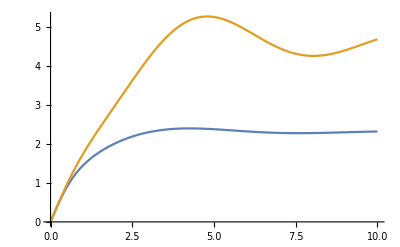

InterpolatingFunction[…]

InterpolatingFunction[…]

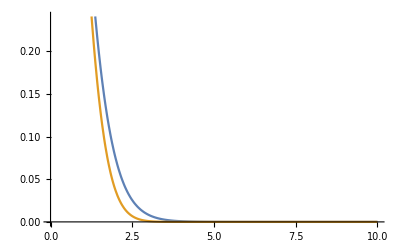

```mathematica
{MATgamTCLa1[[1]],MATgamTCLa1[[2]]}//MatrixForm
γ2a1MAT=Transpose[{MATgamTCLa1[[1]],MATgamTCLa1[[2]]}];
γ4a1MAT=Transpose[{MATgamTCLa1[[1]],MATgamTCLa1[[3]]}];
ListLinePlot[{γ2a1MAT,γ4a1MAT}]
γ2a1f=Interpolation[γ2a1MAT]
γ4a1f=Interpolation[γ4a1MAT]
ρTCL2MATa1[t_]:=Exp[-NIntegrate[γ2a1f[u],{u,0,t}]]
ρTCL4MATa1[t_]:=Exp[-NIntegrate[γ4a1f[u],{u,0,t}]]
Plot[{ρTCL2MATa1[t],ρTCL4MATa1[t]},{t,0,10}]
```

```mathematica
a
```

1

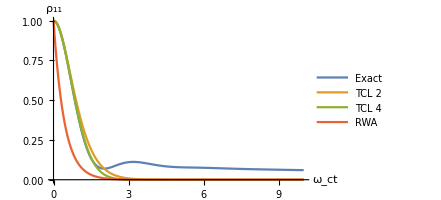

```mathematica
Plot[{ρ11a1[t],ρTCL2[t,a,η],ρTCL4MATa1[t],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

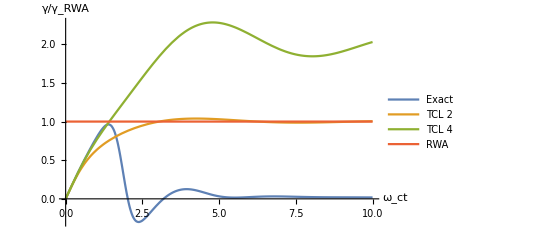

```mathematica
Plot[{(-ρ11pts1'[t]/ρ11pts1[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γ4a1f[t]/(2 π a η Exp[-a]),1},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

### Now with a = 0.5

0.5

{{0,1},{0.01,0.9999},{0.11,0.988},{0.21,0.957203},{0.31,0.909906},{0.41,0.849565},{0.51,0.780211},{0.61,0.70597},{0.71,0.630687},{0.81,0.557662},{0.91,0.489515},{1.01,0.428149},{1.11,0.374771},{1.21,0.329972},{1.31,0.293819},{1.41,0.26596},{1.51,0.245735},{1.61,0.232271},{1.71,0.224571},{1.81,0.221592},{1.91,0.222305},{2.01,0.225739},{2.11,0.231021},{2.21,0.237391},{2.31,0.244217},{2.41,0.250997},{2.51,0.257353},{2.61,0.263022},{2.71,0.267844},{2.81,0.271743},{2.91,0.274715},{3.01,0.276809},{3.11,0.278112},{3.21,0.278737},{3.31,0.278811},{3.41,0.278463},{3.51,0.277818},{3.61,0.27699},{3.71,0.276081},{3.81,0.275174},{3.91,0.274337},{4.01,0.273619},{4.11,0.273054},{4.21,0.272662},{4.31,0.27245},{4.41,0.272415},{4.51,0.272545},{4.61,0.272826},{4.71,0.273236},{4.81,0.273753},{4.91,0.274357},{5.01,0.275025},{5.11,0.275737},{5.21,0.276477},{5.31,0.277229},{5.41,0.277982},{5.51,0.278726},{5.61,0.279454},{5.71,0.280163},{5.81,0.28085},{5.91,0.281515},{6.01,0.282158},{6.11,0.28278},{6.21,0.283385},{6.31,0.283975},{6.41,0.284553},{6.51,0.285122},{6.61,0.285684},{6.71,0.286241},{6.81,0.286795},{6.91,0.287349},{7.01,0.287902},{7.11,0.288457},{7.21,0.289012},{7.31,0.289568},{7.41,0.290125},{7.51,0.290683},{7.61,0.291241},{7.71,0.291797},{7.81,0.292353},{7.91,0.292906},{8.01,0.293457},{8.11,0.294004},{8.21,0.294548},{8.31,0.295087},{8.41,0.29562},{8.51,0.296149},{8.61,0.296672},{8.71,0.29719},{8.81,0.297701},{8.91,0.298206},{9.01,0.298705},{9.11,0.299198},{9.21,0.299685},{9.31,0.300165},{9.41,0.30064},{9.51,0.301108},{9.61,0.30157},{9.71,0.302025},{9.81,0.302475},{9.91,0.302918},{10.1,0.303743},{12.1,0.311036},{14.1,0.315783},{16.1,0.31824},{18.1,0.318842},{20.1,0.318099},{22.1,0.31653},{24.1,0.314607},{26.1,0.312718},{28.1,0.311146},{30.1,0.310063},{32.1,0.309529},{34.1,0.309517},{36.1,0.309926},{38.1,0.310618}}

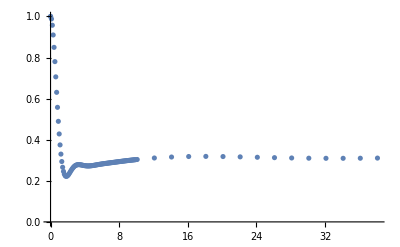

InterpolatingFunction[…]

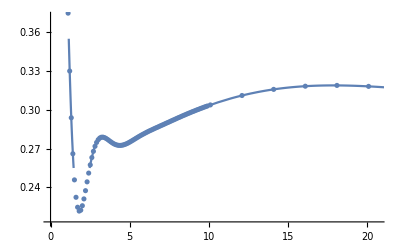

```mathematica
a=0.5
η=1;
T=40;
ρ11ptsa0d5=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,40,2,a,η]]
(*,ρ11pts[100,200,10,a,η]]*)

ListPlot[{ρ11ptsa0d5},PlotRange->All]
ρ11a0d5=Interpolation[ρ11ptsa0d5]
Show[{ListPlot[ρ11ptsa0d5],Plot[ρ11a0d5[t],{t,0,T}]}]
```

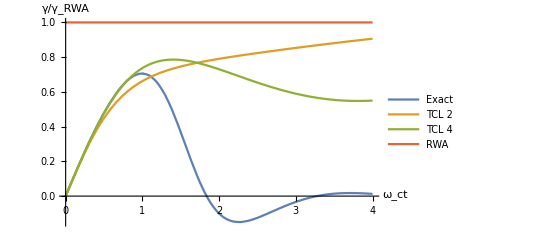

```mathematica
Plot[{(-ρ11a0d5'[t]/ρ11a0d5[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,4},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.5}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

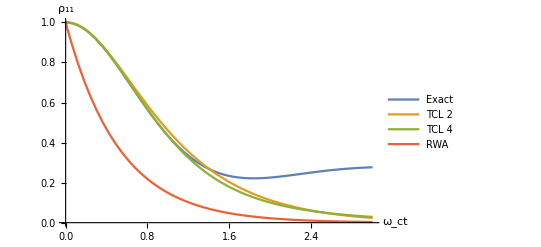

```mathematica
Plot[{ρ11a0d5[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,3},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

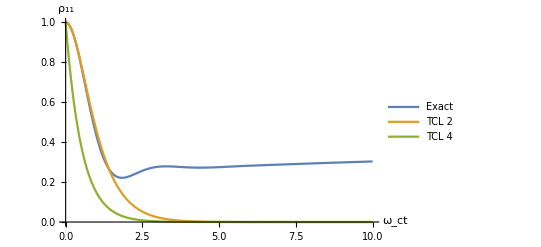

```mathematica
Plot[{ρ11a0d5[t],ρTCL2[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->{"Exact","TCL 2","TCL 4","RWA"},AxesLabel->{"ω_ct","ρ_11"}]
```

```mathematica
ρTCL4[3,a,η]
```

0.028733

```mathematica
MATgamTCLa0d5=Import["/Users/jgarcian/Desktop/gamTCLa0d5.xlsx"]
```

{{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.},{0.,0.198597,0.389078,0.564731,0.721158,0.856467,0.970892,1.06612,1.14459,1.20898,1.26189,1.30557,1.34198,1.37269,1.39897,1.42182,1.442,1.46014,1.47669,1.49201,1.50637,1.51999,1.53302,1.54558,1.55778,1.56967,1.5813,1.59273,1.60396,1.61503,1.62594,1.63671,1.64733,1.65781,1.66816,1.67836,1.68842,1.69833,1.70809,1.71769,1.72712,1.73639,1.74549,1.75441,1.76315,1.7717,1.78006,1.78823,1.7962,1.80396,1.81153,1.81888,1.82603,1.83296,1.83968,1.84618,1.85247,1.85854,1.8644,1.87003,1.87545,1.88065,1.88564,1.89041,1.89496,1.8993,1.90343,1.90735,1.91106,1.91456,1.91787,1.92097,1.92388,1.92659,1.92911,1.93145,1.9336,1.93557,1.93737,1.939,1.94046,1.94175,1.94289,1.94387,1.9447,1.94539,1.94594,1.94635,1.94664,1.94679,1.94683,1.94675,1.94656,1.94627,1.94587,1.94538,1.9448,1.94413,1.94339,1.94257,1.94167},{0.,0.199251,0.394028,0.57999,0.753149,0.910166,1.04862,1.16716,1.26547,1.34413,1.4044,1.44796,1.47672,1.49268,1.49779,1.49388,1.48263,1.46554,1.44394,1.41897,1.39164,1.36279,1.33315,1.30334,1.27387,1.24516,1.21759,1.19145,1.16699,1.1444,1.12386,1.1055,1.08941,1.07569,1.06438,1.05552,1.04915,1.04527,1.04387,1.04496,1.04851,1.05448,1.06284,1.07354,1.08654,1.10177,1.11918,1.13869,1.16025,1.18376,1.20916,1.23635,1.26527,1.29581,1.3279,1.36143,1.39631,1.43246,1.46977,1.50815,1.54749,1.5877,1.62869,1.67035,1.71257,1.75528,1.79836,1.84171,1.88526,1.92889,1.97251,2.01604,2.05938,2.10244,2.14514,2.18739,2.22912,2.27024,2.31067,2.35035,2.3892,2.42716,2.46416,2.50013,2.53503,2.56879,2.60137,2.63272,2.66279,2.69154,2.71894,2.74496,2.76955,2.79271,2.8144,2.8346,2.85331,2.87051,2.88619,2.90035,2.91299}}}

```mathematica
MATCLa0d5=MATgamTCLa0d5[[1]];
```

(0. | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1. | 1.1 | 1.2 | 1.3 | 1.4 | 1.5 | 1.6 | 1.7 | 1.8 | 1.9 | 2. | 2.1 | 2.2 | 2.3 | 2.4 | 2.5 | 2.6 | 2.7 | 2.8 | 2.9 | 3. | 3.1 | 3.2 | 3.3 | 3.4 | 3.5 | 3.6 | 3.7 | 3.8 | 3.9 | 4. | 4.1 | 4.2 | 4.3 | 4.4 | 4.5 | 4.6 | 4.7 | 4.8 | 4.9 | 5. | 5.1 | 5.2 | 5.3 | 5.4 | 5.5 | 5.6 | 5.7 | 5.8 | 5.9 | 6. | 6.1 | 6.2 | 6.3 | 6.4 | 6.5 | 6.6 | 6.7 | 6.8 | 6.9 | 7. | 7.1 | 7.2 | 7.3 | 7.4 | 7.5 | 7.6 | 7.7 | 7.8 | 7.9 | 8. | 8.1 | 8.2 | 8.3 | 8.4 | 8.5 | 8.6 | 8.7 | 8.8 | 8.9 | 9. | 9.1 | 9.2 | 9.3 | 9.4 | 9.5 | 9.6 | 9.7 | 9.8 | 9.9 | 10.
0. | 0.198597 | 0.389078 | 0.564731 | 0.721158 | 0.856467 | 0.970892 | 1.06612 | 1.14459 | 1.20898 | 1.26189 | 1.30557 | 1.34198 | 1.37269 | 1.39897 | 1.42182 | 1.442 | 1.46014 | 1.47669 | 1.49201 | 1.50637 | 1.51999 | 1.53302 | 1.54558 | 1.55778 | 1.56967 | 1.5813 | 1.59273 | 1.60396 | 1.61503 | 1.62594 | 1.63671 | 1.64733 | 1.65781 | 1.66816 | 1.67836 | 1.68842 | 1.69833 | 1.70809 | 1.71769 | 1.72712 | 1.73639 | 1.74549 | 1.75441 | 1.76315 | 1.7717 | 1.78006 | 1.78823 | 1.7962 | 1.80396 | 1.81153 | 1.81888 | 1.82603 | 1.83296 | 1.83968 | 1.84618 | 1.85247 | 1.85854 | 1.8644 | 1.87003 | 1.87545 | 1.88065 | 1.88564 | 1.89041 | 1.89496 | 1.8993 | 1.90343 | 1.90735 | 1.91106 | 1.91456 | 1.91787 | 1.92097 | 1.92388 | 1.92659 | 1.92911 | 1.93145 | 1.9336 | 1.93557 | 1.93737 | 1.939 | 1.94046 | 1.94175 | 1.94289 | 1.94387 | 1.9447 | 1.94539 | 1.94594 | 1.94635 | 1.94664 | 1.94679 | 1.94683 | 1.94675 | 1.94656 | 1.94627 | 1.94587 | 1.94538 | 1.9448 | 1.94413 | 1.94339 | 1.94257 | 1.94167)

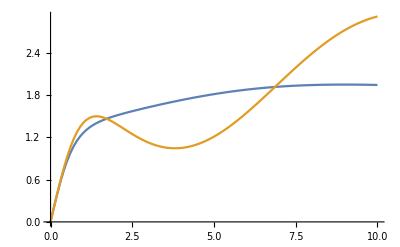

InterpolatingFunction[…]

InterpolatingFunction[…]

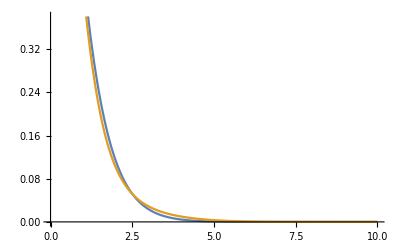

```mathematica
{MATCLa0d5[[1]],MATCLa0d5[[2]]}//MatrixForm
γ2a0d5MAT=Transpose[{MATCLa0d5[[1]],MATCLa0d5[[2]]}];
γ4a0d5MAT=Transpose[{MATCLa0d5[[1]],MATCLa0d5[[3]]}];
ListLinePlot[{γ2a0d5MAT,γ4a0d5MAT}]

γ2a0d5f=Interpolation[γ2a0d5MAT]
γ4a0d5f=Interpolation[γ4a0d5MAT]
ρTCL2MATa0d5[t_]:=Exp[-NIntegrate[γ2a0d5f[u],{u,0,t}]]
ρTCL4MATa0d5[t_]:=Exp[-NIntegrate[γ4a0d5f[u],{u,0,t}]]
Plot[{ρTCL2MATa0d5[t],ρTCL4MATa0d5[t]},{t,0,10}]
```

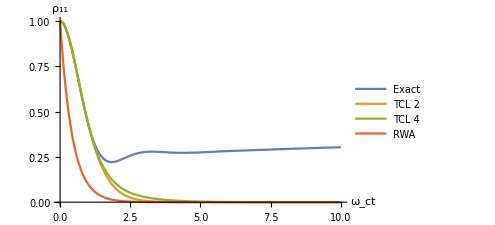

```mathematica
Plot[{ρ11a0d5[t],ρTCL2[t,a,η],ρTCL4MATa0d5[t],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

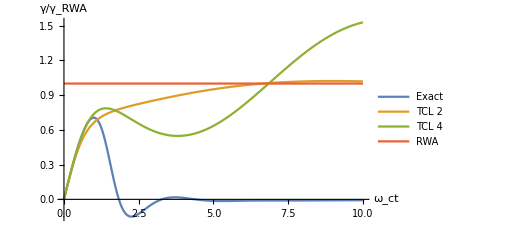

```mathematica
Plot[{(-ρ11a0d5'[t]/ρ11a0d5[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γ4a0d5f[t]/(2 π a η Exp[-a]),1},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.4}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

```mathematica
ρ11a0d5[20]
```

0.318161

```mathematica
ρ11[100,0.9,η]
ρ11[100,0.8,η]
ρ11[100,0.7,η]
ρ11[100,0.6,η]
ρ11[100,0.5,η]
ρ11[100,0.4,η]
ρ11[100,0.3,η]
ρ11[100,0.2,η]
```

0.0883302

0.145771

0.203572

0.258454

0.311863

0.363088

0.411366

0.456353

```mathematica
__________________
```

0

{{0,1},{0.01,0.9999},{0.11,0.988021},{0.21,0.957474},{0.31,0.911129},{0.41,0.853059},{0.51,0.787897},{0.61,0.720225},{0.71,0.65411},{0.81,0.592819},{0.91,0.538697},{1.01,0.493187},{1.11,0.456915},{1.21,0.429835},{1.31,0.411384},{1.41,0.400637},{1.51,0.39645},{1.61,0.397578},{1.71,0.402777},{1.81,0.410875},{1.91,0.420821},{2.01,0.431723},{2.11,0.442854},{2.21,0.453659},{2.31,0.463742},{2.41,0.472849},{2.51,0.480851},{2.61,0.487712},{2.71,0.493477},{2.81,0.498241},{2.91,0.502133},{3.01,0.5053},{3.11,0.507892},{3.21,0.510054},{3.31,0.511913},{3.41,0.51358},{3.51,0.515146},{3.61,0.516678},{3.71,0.518224},{3.81,0.519815},{3.91,0.521465},{4.01,0.523175},{4.11,0.524938},{4.21,0.526738},{4.31,0.528557},{4.41,0.530373},{4.51,0.532167},{4.61,0.533917},{4.71,0.535607},{4.81,0.537221},{4.91,0.538748},{5.01,0.54018},{5.11,0.541509},{5.21,0.542734},{5.31,0.543854},{5.41,0.54487},{5.51,0.545785},{5.61,0.546602},{5.71,0.547326},{5.81,0.547962},{5.91,0.548515},{6.01,0.54899},{6.11,0.549392},{6.21,0.549725},{6.31,0.549993},{6.41,0.5502},{6.51,0.55035},{6.61,0.550445},{6.71,0.550488},{6.81,0.550483},{6.91,0.55043},{7.01,0.550333},{7.11,0.550193},{7.21,0.550013},{7.31,0.549795},{7.41,0.54954},{7.51,0.549251},{7.61,0.54893},{7.71,0.548579},{7.81,0.5482},{7.91,0.547795},{8.01,0.547367},{8.11,0.546918},{8.21,0.546449},{8.31,0.545964},{8.41,0.545464},{8.51,0.544951},{8.61,0.544428},{8.71,0.543896},{8.81,0.543358},{8.91,0.542814},{9.01,0.542269},{9.11,0.541722},{9.21,0.541175},{9.31,0.540631},{9.41,0.540091},{9.51,0.539556},{9.61,0.539028},{9.71,0.538508},{9.81,0.537998},{9.91,0.537497},{10.1,0.53658},{12.1,0.530711},{14.1,0.532081},{16.1,0.536512},{18.1,0.539035},{20.1,0.538092},{22.1,0.535602},{24.1,0.534239},{26.1,0.534929},{28.1,0.536527},{30.1,0.537356},{32.1,0.536824},{34.1,0.535711},{36.1,0.535166},{38.1,0.535591},{100,0.536185},{110,0.536065},{120,0.535998},{130,0.53602},{140,0.53609},{150,0.536141},{160,0.536136},{170,0.536093},{180,0.536054},{190,0.53605},{200,0.536078},{210,0.536109},{220,0.536116},{230,0.536098},{240,0.536074},{250,0.536065},{260,0.536076},{270,0.536096},{280,0.536105},{290,0.536098},{300,0.536082},{310,0.536073},{320,0.536077},{330,0.53609},{340,0.536099},{350,0.536097},{360,5.73044×10^-11},{370,5.14112×10^-11},{380,4.62563×10^-11},{390,4.17316×10^-11},{400,3.77468×10^-11}}

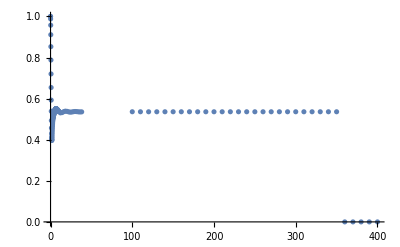

InterpolatingFunction[…]

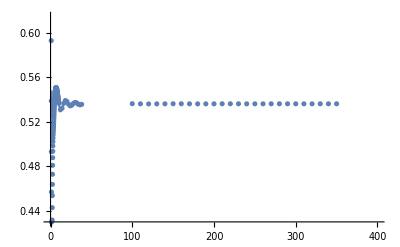

```mathematica
a=0
η=1;
T=40;
ρ11ptsa0=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,40,2,a,η],ρ11pts[100,400,10,a,η]]

ListPlot[{ρ11ptsa0},PlotRange->All]
ρ11a0=Interpolation[ρ11ptsa0]
Show[{ListPlot[ρ11ptsa0],Plot[ρ11a0[t],{t,0,T}]}]
```

```mathematica
ρ11[356,0,η]
```

0.536078

```mathematica
a
```

0

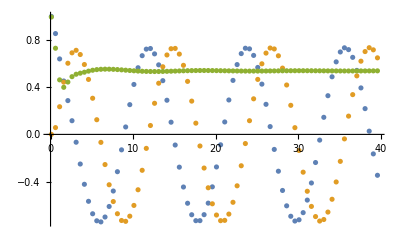

```mathematica
fse[s_,a_,η_]:=η(-ⅈ +ⅇ^(-(ⅈ s+a)) (s-ⅈ a)Gamma[0,-ⅈ (s-ⅈ a)])
c1[t_,a_,η_]:=ResourceFunction["NInverseLaplaceTransform"][1/(s+fse[s,a,η]),s,t]
c11pts[t0_,tf_,step_,a_,η_]:=
Thread[{Table[i,{i,t0,tf,step}],Table[c1[i,a,η],{i,t0,tf,step}]}]
tf=40;
step=0.5;
pointsc11=c11pts[0.1,tf,step,a,η];

Rec11=pointsc11/. {x_,y_}:>{x,Re[y]};
Imc11=pointsc11/. {x_,y_}:>{x,Im[y]};
Normc11=pointsc11/. {x_,y_}:>{x,Norm[y]^2};
ListPlot[{Rec11,Imc11,Normc11}]
```

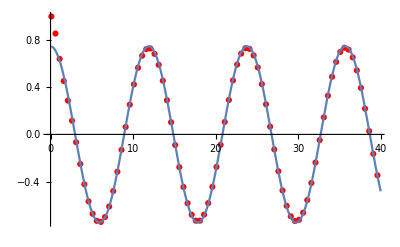

FittedModel[0.743135 Cos[0.528053 x]]

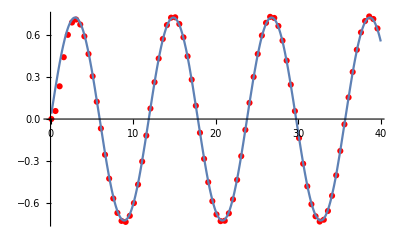

FittedModel[0.723628 Sin[0.528029 x]]

```mathematica
rescos=NonlinearModelFit[Rec11,A Cos[b x],{{A,1},{b,10}},x,Method->{"NMinimize",{Method->"DifferentialEvolution"}}];
Show[ListPlot[Rec11,PlotStyle->Red],Plot[rescos[x],{x,0.1,40}]]
rescos

ressin=NonlinearModelFit[Imc11,A Sin[b x],{{A,1},{b,10}},x,Method->{"NMinimize",{Method->"DifferentialEvolution"}}];
Show[ListPlot[Imc11,PlotStyle->Red],Plot[ressin[x],{x,0.1,40}]]
ressin
```

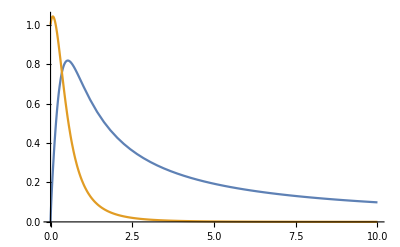

```mathematica
Plot[{Re[1/(s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s])],Im[1/(s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s])]},{s,0,10}]
```

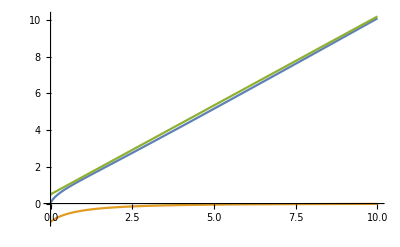

```mathematica
Plot[{Re[s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s]],Im[s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s]],(0.97s+0.5)},{s,0,10}]
```

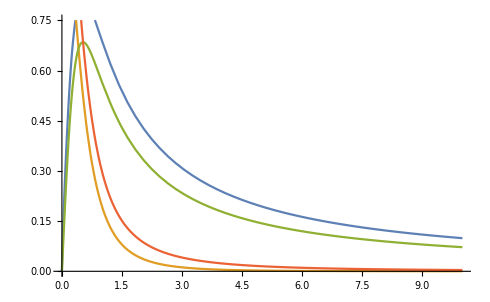

```mathematica
Plot[{Re[1/(s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s])],Im[1/(s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s])],Re[0.7236275261044905/(s-ⅈ 0.5280287285430189)],Im[0.7236275261044905/(s-ⅈ 0.5280287285430189)]},{s,0,10}]
```

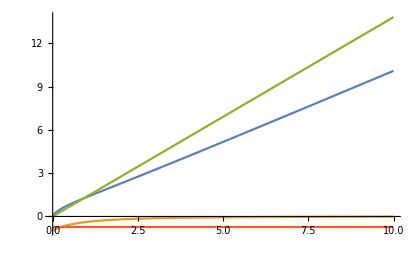

```mathematica
Plot[{Re[s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s]],Im[s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s]],Re[(s-ⅈ 0.5280287285430189)/0.7236275261044905],Im[(s-ⅈ 0.5280287285430189)/0.7236275261044905]},{s,0,10}]
```

```mathematica
Gamma[0,-ⅈ 0]
```

∞

```mathematica
InverseLaplaceTransform[1/(s+1),s,t]
```

ⅇ^-t

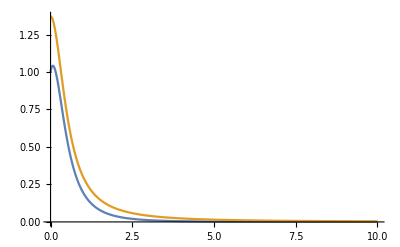

```mathematica
Plot[{Im[1/(s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s])],Im[0.7236275261044905/(s-ⅈ 0.5280287285430189)]},{s,0,10},PlotRange->All]
```

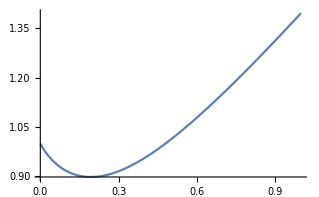

```mathematica
Plot[{Norm[s+-ⅈ+ⅇ^(-ⅈ s) s Gamma[0,-ⅈ s]]},{s,0,1}]
```

## NOW with eta non one

1

{{0,1},{0.01,0.99995},{0.11,0.99398},{0.21,0.978346},{0.31,0.953784},{0.41,0.921373},{0.51,0.882411},{0.61,0.838283},{0.71,0.790364},{0.81,0.739941},{0.91,0.688172},{1.01,0.636067},{1.11,0.58448},{1.21,0.534115},{1.31,0.485537},{1.41,0.439183},{1.51,0.395379},{1.61,0.354349},{1.71,0.316233},{1.81,0.281097},{1.91,0.248948},{2.01,0.21974},{2.11,0.193387},{2.21,0.169771},{2.31,0.148748},{2.41,0.13016},{2.51,0.113833},{2.61,0.0995895},{2.71,0.0872476},{2.81,0.0766278},{2.91,0.067554},{3.01,0.0598572},{3.11,0.0533763},{3.21,0.0479598},{3.31,0.043467},{3.41,0.0397683},{3.51,0.0367453},{3.61,0.0342912},{3.71,0.0323104},{3.81,0.0307181},{3.91,0.0294399},{4.01,0.0284112},{4.11,0.0275764},{4.21,0.0268884},{4.31,0.0263076},{4.41,0.0258012},{4.51,0.0253429},{4.61,0.0249114},{4.71,0.0244903},{4.81,0.0240675},{4.91,0.023634},{5.01,0.023184},{5.11,0.0227141},{5.21,0.0222227},{5.31,0.0217099},{5.41,0.0211771},{5.51,0.0206263},{5.61,0.0200605},{5.71,0.0194827},{5.81,0.0188965},{5.91,0.0183053},{6.01,0.0177126},{6.11,0.0171215},{6.21,0.0165352},{6.31,0.0159564},{6.41,0.0153877},{6.51,0.014831},{6.61,0.0142882},{6.71,0.0137608},{6.81,0.0132499},{6.91,0.0127564},{7.01,0.0122809},{7.11,0.0118237},{7.21,0.0113849},{7.31,0.0109645},{7.41,0.0105621},{7.51,0.0101775},{7.61,0.00981007},{7.71,0.00945927},{7.81,0.00912445},{7.91,0.00880489},{8.01,0.00849988},{8.11,0.00820865},{8.21,0.00793047},{8.31,0.00766458},{8.41,0.00741028},{8.51,0.00716685},{8.61,0.00693363},{8.71,0.00670999},{8.81,0.00649534},{8.91,0.00628911},{9.01,0.00609079},{9.11,0.0058999},{9.21,0.005716},{9.31,0.00553869},{9.41,0.0053676},{9.51,0.0052024},{9.61,0.00504277},{9.71,0.00488845},{9.81,0.00473918},{9.91,0.00459474},{10.1,0.00433286},{11.1,0.00318652},{12.1,0.00234987},{13.1,0.00174009},{14.1,0.00129372},{15.1,0.00096468},{16.1,0.000720833},{17.1,0.000539523},{18.1,0.000404383},{19.1,0.000303448},{20.1,0.000227937},{21.1,0.00017138},{22.1,0.000128983},{23.1,0.0000971836},{24.1,0.0000733245},{25.1,0.0000554194},{26.1,0.0000419813},{27.1,0.0000318949},{28.1,0.0000243234},{29.1,0.0000186384},{30.1,0.0000143678},{31.1,0.000011157},{32.1,8.73993×10^-6},{33.1,6.91683×10^-6},{34.1,5.53795×10^-6},{35.1,4.4911×10^-6},{36.1,3.69235×10^-6},{37.1,3.07898×10^-6},{38.1,2.60419×10^-6},{39.1,2.2331×10^-6}}

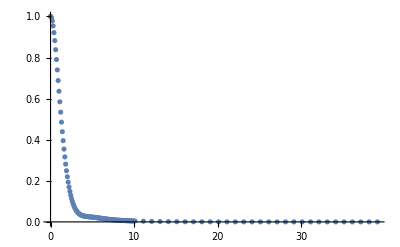

InterpolatingFunction[…]

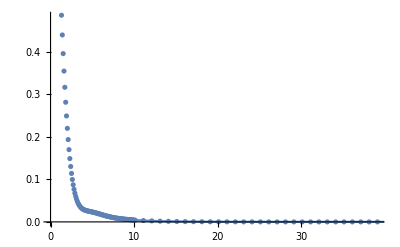

```mathematica
a=1
η=0.5;
T=40;
ρ11ptseta05=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.1,a,η],ρ11pts[10.1,40,1,a,η]]
(*,ρ11pts[100,200,10,a,η]]*)

ListPlot[{ρ11ptseta05},PlotRange->All]
ρ11eta05=Interpolation[ρ11ptseta05]
Show[{ListPlot[ρ11ptseta05],Plot[ρ11eta05[t],{t,0,T}]}]
```

```mathematica
Plot[{ρ11eta05[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

$Aborted

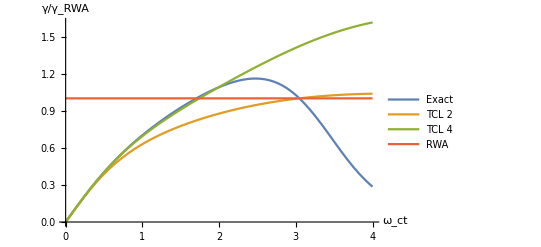

```mathematica
Plot[{(-ρ11eta05'[t]/ρ11eta05[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γTCL4[t,a,η]/(2 π a η Exp[-a]),1},{t,0,4},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.4}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

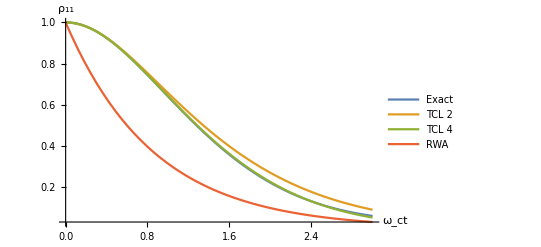

```mathematica
Plot[{ρ11eta05[t],ρTCL2[t,a,η],ρTCL4[t,a,η],Exp[-2 π a η Exp[-a]t]},{t,0,3},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

```mathematica
MATgamTCLeta05=Import["/Users/jgarcian/Desktop/ganmmaa1eta05.xlsx"][[1]]
```

{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.},{0.,0.0995044,0.196136,0.287489,0.371926,0.448659,0.517619,0.57925,0.634277,0.68353,0.727827,0.767908,0.804407,0.837854,0.868676,0.897216,0.923745,0.948475,0.971576,0.993178,1.01339,1.03229,1.04995,1.06642,1.08175,1.09598,1.10915,1.12129,1.13243,1.14259,1.15182,1.16014,1.16757,1.17416,1.17993,1.18491,1.18914,1.19266,1.1955,1.19769,1.19928,1.2003,1.20079,1.20079,1.20035,1.19949,1.19826,1.1967,1.19484,1.19273,1.19041,1.18789,1.18524,1.18246,1.17961,1.17671,1.17379,1.17087,1.16799,1.16516,1.16242,1.15977,1.15724,1.15485,1.1526,1.15051,1.14859,1.14685,1.1453,1.14393,1.14276,1.14177,1.14098,1.14038,1.13995,1.13971,1.13964,1.13974,1.13998,1.14038,1.14091,1.14156,1.14232,1.14318,1.14413,1.14515,1.14623,1.14736,1.14852,1.1497,1.15089,1.15209,1.15326,1.15442,1.15554,1.15661,1.15764,1.1586,1.1595,1.16033,1.16107},{0.,0.0996691,0.197408,0.291548,0.380861,0.464633,0.542623,0.614965,0.682048,0.744404,0.802628,0.857311,0.909014,0.958239,1.00542,1.05094,1.09509,1.13812,1.18023,1.22154,1.26215,1.30212,1.34147,1.38018,1.41822,1.45554,1.49206,1.5277,1.56237,1.59595,1.62834,1.65944,1.68913,1.71732,1.74391,1.7688,1.79191,1.81317,1.83253,1.84992,1.86531,1.87868,1.89003,1.89935,1.90667,1.91202,1.91544,1.91699,1.91674,1.91478,1.9112,1.9061,1.89958,1.89177,1.8828,1.87278,1.86185,1.85016,1.83783,1.825,1.81181,1.79839,1.78488,1.7714,1.75807,1.74502,1.73234,1.72015,1.70854,1.69759,1.68739,1.678,1.66947,1.66187,1.65523,1.64959,1.64495,1.64133,1.63874,1.63716,1.63657,1.63697,1.6383,1.64053,1.64362,1.6475,1.65212,1.65742,1.66332,1.66976,1.67665,1.68392,1.6915,1.69929,1.70722,1.71522,1.7232,1.73108,1.73879,1.74627,1.75345}}

(0. | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1. | 1.1 | 1.2 | 1.3 | 1.4 | 1.5 | 1.6 | 1.7 | 1.8 | 1.9 | 2. | 2.1 | 2.2 | 2.3 | 2.4 | 2.5 | 2.6 | 2.7 | 2.8 | 2.9 | 3. | 3.1 | 3.2 | 3.3 | 3.4 | 3.5 | 3.6 | 3.7 | 3.8 | 3.9 | 4. | 4.1 | 4.2 | 4.3 | 4.4 | 4.5 | 4.6 | 4.7 | 4.8 | 4.9 | 5. | 5.1 | 5.2 | 5.3 | 5.4 | 5.5 | 5.6 | 5.7 | 5.8 | 5.9 | 6. | 6.1 | 6.2 | 6.3 | 6.4 | 6.5 | 6.6 | 6.7 | 6.8 | 6.9 | 7. | 7.1 | 7.2 | 7.3 | 7.4 | 7.5 | 7.6 | 7.7 | 7.8 | 7.9 | 8. | 8.1 | 8.2 | 8.3 | 8.4 | 8.5 | 8.6 | 8.7 | 8.8 | 8.9 | 9. | 9.1 | 9.2 | 9.3 | 9.4 | 9.5 | 9.6 | 9.7 | 9.8 | 9.9 | 10.
0. | 0.0995044 | 0.196136 | 0.287489 | 0.371926 | 0.448659 | 0.517619 | 0.57925 | 0.634277 | 0.68353 | 0.727827 | 0.767908 | 0.804407 | 0.837854 | 0.868676 | 0.897216 | 0.923745 | 0.948475 | 0.971576 | 0.993178 | 1.01339 | 1.03229 | 1.04995 | 1.06642 | 1.08175 | 1.09598 | 1.10915 | 1.12129 | 1.13243 | 1.14259 | 1.15182 | 1.16014 | 1.16757 | 1.17416 | 1.17993 | 1.18491 | 1.18914 | 1.19266 | 1.1955 | 1.19769 | 1.19928 | 1.2003 | 1.20079 | 1.20079 | 1.20035 | 1.19949 | 1.19826 | 1.1967 | 1.19484 | 1.19273 | 1.19041 | 1.18789 | 1.18524 | 1.18246 | 1.17961 | 1.17671 | 1.17379 | 1.17087 | 1.16799 | 1.16516 | 1.16242 | 1.15977 | 1.15724 | 1.15485 | 1.1526 | 1.15051 | 1.14859 | 1.14685 | 1.1453 | 1.14393 | 1.14276 | 1.14177 | 1.14098 | 1.14038 | 1.13995 | 1.13971 | 1.13964 | 1.13974 | 1.13998 | 1.14038 | 1.14091 | 1.14156 | 1.14232 | 1.14318 | 1.14413 | 1.14515 | 1.14623 | 1.14736 | 1.14852 | 1.1497 | 1.15089 | 1.15209 | 1.15326 | 1.15442 | 1.15554 | 1.15661 | 1.15764 | 1.1586 | 1.1595 | 1.16033 | 1.16107)

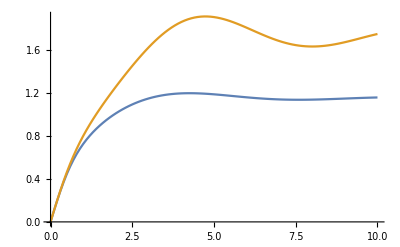

InterpolatingFunction[…]

InterpolatingFunction[…]

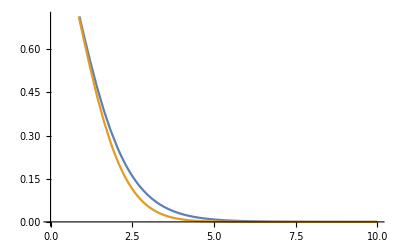

```mathematica
{MATgamTCLeta05[[1]],MATgamTCLeta05[[2]]}//MatrixForm
γ2eta05MAT=Transpose[{MATgamTCLeta05[[1]],MATgamTCLeta05[[2]]}];
γ4eta05MAT=Transpose[{MATgamTCLeta05[[1]],MATgamTCLeta05[[3]]}];
ListLinePlot[{γ2eta05MAT,γ4eta05MAT}]

γ2eta05f=Interpolation[γ2eta05MAT]
γ4eta05f=Interpolation[γ4eta05MAT]
ρTCL2MATeta05[t_]:=Exp[-NIntegrate[γ2eta05f[u],{u,0,t}]]
ρTCL4MATeta05[t_]:=Exp[-NIntegrate[γ4eta05f[u],{u,0,t}]]
Plot[{ρTCL2MATeta05[t],ρTCL4MATeta05[t]},{t,0,10}]
```

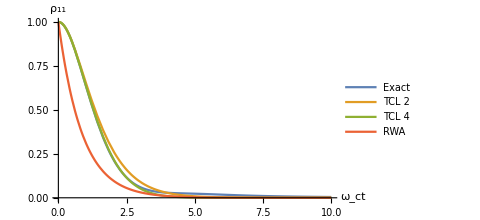

```mathematica
Plot[{ρ11eta05[t],ρTCL2[t,a,η],ρTCL4MATeta05[t],Exp[-2 π a η Exp[-a]t]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.7}],AxesLabel->{"ω_ct","ρ_11"}]
```

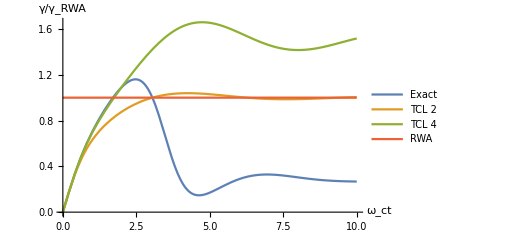

```mathematica
Plot[{(-ρ11eta05'[t]/ρ11eta05[t])/(2 π a η Exp[-a]),γTCL2[t,a,η]/(2 π a η Exp[-a]),γ4eta05f[t]/(2 π a η Exp[-a]),1},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Exact","TCL 2","TCL 4","RWA"},{0.85,0.4}],AxesLabel->{"ω_ct","γ/γ_RWA"}]
```

```mathematica
___________________________
```

## Now for a=2

```mathematica
a=2
T=100
ρ11ptsLista2=Join[{{0,1}},ρ11pts[0.01,3,0.1,a,η],ρ11pts[3.01,10,0.5,a,η],ρ11pts[10,100,10,a,η]]
(*,ρ11pts[10,20,1,a,η],ρ11pts[21,100,10,a,η],ρ11pts[100,200,100,a,η]]*)
ListPlot[{ρ11ptsLista2},PlotRange->All]
ρ11a2=Interpolation[ρ11ptsLista2]
```

2

100

$Aborted

-Graphics-

Interpolation::innd: First argument in ρ11ptsLista2 does not contain a list of data and coordinates.

Interpolation[ρ11ptsLista2]

{{0,1},{0.01,0.9999},{0.11,0.987973},{0.21,0.956855},{0.31,0.908343},{0.41,0.845126},{0.51,0.770512},{0.61,0.688132},{0.71,0.601667},{0.81,0.514611},{0.91,0.430094},{1.01,0.350752},{1.11,0.278657},{1.21,0.215276},{1.31,0.161487},{1.41,0.117607},{1.51,0.0834603},{1.61,0.0584517},{1.71,0.0416587},{1.81,0.0319251},{1.91,0.0279542},{2.01,0.0283965},{2.11,0.0319278},{2.21,0.0373144},{2.31,0.0434646},{2.41,0.0494645},{2.51,0.0545991},{2.61,0.058359},{2.71,0.060435},{2.81,0.0607016},{2.91,0.0591932},{3.01,0.0560744},{3.51,0.0270794},{4.01,0.00386667},{4.51,0.000907304},{5.01,0.00616791},{5.51,0.00708875},{6.01,0.00347283},{6.51,0.000664218},{7.01,0.000626513},{7.51,0.00147967},{8.01,0.0014937},{8.51,0.000855152},{9.01,0.000431866},{9.51,0.0004421},{10,0.000537225},{20,0.0000288842},{30,3.19453×10^-6},{40,6.49423×10^-7},{50,2.18901×10^-7},{60,9.75676×10^-8},{70,5.05073×10^-8},{80,2.87874×10^-8},{90,1.76025×10^-8},{100,1.13651×10^-8}}

InterpolatingFunction[…]

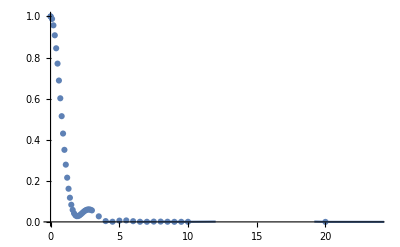

```mathematica
ρ11ptsLista2={{0,1},{0.01,0.9999000049997944},{0.11,0.9879728430254759},{0.21000000000000002,0.9568551521830402},{0.31000000000000005,0.9083434062586985},{0.41000000000000003,0.8451263018513969},{0.51,0.7705117478437973},{0.6100000000000001,0.6881318790418266},{0.7100000000000001,0.6016667327250639},{0.81,0.51461097538404},{0.91,0.4300937484121429},{1.01,0.35075246154519885},{1.11,0.27865665494781905},{1.2100000000000002,0.21527610331811803},{1.31,0.16148666032395886},{1.4100000000000001,0.11760712165102463},{1.51,0.08346031534880244},{1.61,0.05845166571803243},{1.7100000000000002,0.04165866445838928},{1.81,0.03192506294744758},{1.9100000000000001,0.027954185886996375},{2.01,0.02839654139151581},{2.11,0.031927824674506854},{2.21,0.03731442673183097},{2.31,0.04346460546030915},{2.41,0.04946449554837361},{2.51,0.05459907262566855},{2.61,0.05835900358128442},{2.71,0.060434977246408526},{2.81,0.06070159873685712},{2.91,0.059193239803761816},{3.01,0.05607437092642453},{3.51,0.027079380836275355},{4.01,0.003866671221792567},{4.51,0.0009073035472851402},{5.01,0.006167906571973661},{5.51,0.007088747366837341},{6.01,0.0034728299708136905},{6.51,0.0006642180179689233},{7.01,0.0006265125045101516},{7.51,0.0014796671543850627},{8.01,0.0014936988830726956},{8.51,0.0008551517055288652},{9.01,0.0004318663615076583},{9.51,0.0004420998940946116},{10,0.0005372253966739474},{20,0.000028884236833859988},{30,3.1945312976546053*^-6},{40,6.494232564054531*^-7},{50,2.1890059266714468*^-7},{60,9.75675781734389*^-8},{70,5.050726500517345*^-8},{80,2.8787395061329194*^-8},
{90,1.760254104800164*^-8},{100,1.1365080067327056*^-8}}
ρ11a2=Interpolation[ρ11ptsLista2]
Show[{ListPlot[ρ11ptsLista2],Plot[ρ11a2[t],{t,0,T}]}]
```

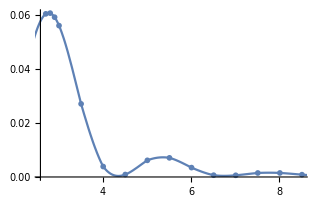

```mathematica
Show[{ListPlot[ρ11ptsLista2[[29;;43]]],Plot[ρ11a2[t],{t,0,9}]}]
```

```mathematica
bww[t_,ω_,η_]:=η ⅇ^-ω((1-ω-I ω t)ExpIntegralEi[ω+I ω t]+(1-ω+I ω t)ExpIntegralEi[ω-I ω t]+2(ω-1)ExpIntegralEi[ω])+2η(1-Cos[ ω t])
γww[t_,ω_,η_]:=bww[t,ω,η]/t
FullSimplify[bww[t,ω,η]]
```

1.-1. Cos[t ω]+0.5 ⅇ^-ω (2 (-1+ω) ExpIntegralEi[ω]+(1-ω+ⅈ t ω) ExpIntegralEi[ω-ⅈ t ω]+(1-ω-ⅈ t ω) ExpIntegralEi[ω+ⅈ t ω])

```mathematica
η=1
```

1

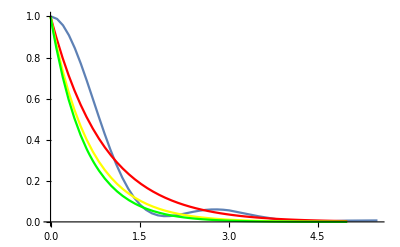

```mathematica
Show[{ListLinePlot[ρ11ptsLista2[[1;;37]],PlotRange->All],Plot[{Exp[-Re[γww[0.123643398284912,a,η]]t],Exp[-Re[γww[3.13107,a,η]]t],Exp[-2π η a ⅇ^(- a)t]},{t,0,5},PlotStyle->{Red,Yellow,Green}]}]
```

```mathematica
Subscript[τ,a]
```

τ_2

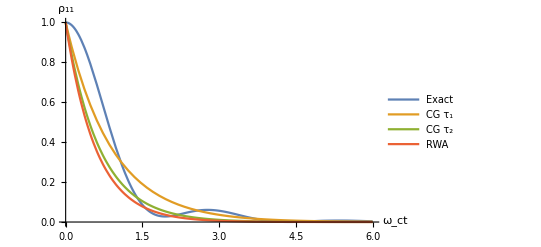

```mathematica
Plot[{ρ11a2[t],Exp[-Re[γww[0.123643398284912,a,η]]t],Exp[-Re[γww[3.13107,a,η]]t],Exp[-2π η a ⅇ^(- a)t]},{t,0,6},PlotLegends->Placed[{"Exact","CG τ_1","CG τ_2","RWA"},{0.85,0.4}],AxesLabel->{"ω_ct","ρ_11"},PlotRange->All]
```

```mathematica
Δρ11Markov[ρ11fun_,T_,a_,η_]:=NIntegrate[Abs[ρ11fun[t]-Exp[-2π η a ⅇ^(- a)t]],{t,0,T}]/T
Δρ11CG[ρ11fun_,τ_,T_,a_,η_]:=NIntegrate[Abs[ρ11fun[t]-Exp[-γww[τ,a,η]t]],{t,0,T}]/T
```

100

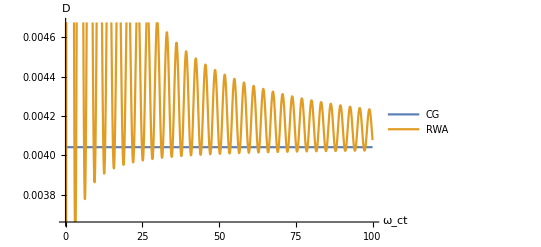

```mathematica
T=100
Plot[{Δρ11Markov[ρ11a2,T,a,η],Δρ11CG[ρ11a2,t,T,a,η]},{t,0,T},AxesLabel->{"ω_ct","D"},PlotLegends->Placed[{"CG","RWA"},{0.85,0.3}]]
```

100

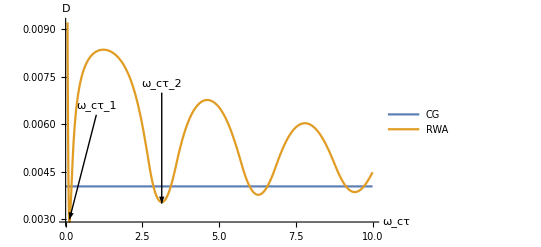

```mathematica
T=100
Plot[{Δρ11Markov[ρ11a2,T,a,η],Δρ11CG[ρ11a2,t,T,a,η]},{t,0,10},AxesLabel->{"ω_cτ","D"},PlotLegends->Placed[{"CG","RWA"},{0.85,0.7}],Epilog->{Arrow[{{1,0.0063},{0.1236433983,0.003}}],Inset["ω_cτ_1",{1,0.0066}],Arrow[{{3.13107,0.007},{3.13107,0.0035}}],Inset["ω_cτ_2",{3.13107,0.0073}]}]
```

{{1,0.280982},{1.12,0.267152},{1.25,0.267152},{1.37,0.222044},{1.5,0.222044},{1.63,0.222044},{1.75,0.160267},{1.88,0.140661},{2,0.123643},{2.13,0.106858},{2.25,0.106858},{2.38,0.0794772},{2.5,0.0687755}}

{{1,6.20404},{1.12,5.54611},{1.25,4.97611},{1.37,4.54591},{1.5,4.15733},{1.63,3.83044},{1.75,3.57152},{1.88,3.32802},{2,3.13107},{2.13,2.94248},{2.25,2.78751},{2.38,2.63704},{2.5,2.51186}}

InterpolatingFunction[…]

InterpolatingFunction[…]

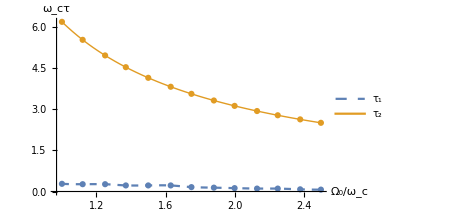

```mathematica
avst1={{1,0.2809824085},{1.12,0.267152},{1.25,0.267152},{1.37,0.222044},{1.5,0.222044},{1.63,0.222044},{1.75,0.160267},{1.88,0.140661},{2,0.1236433983},{2.13,0.106858},{2.25,0.106858},{2.38,0.0794772},{2.5,0.0687755}}
avst2={{1,6.204043436},{1.12,5.54611},{1.25,4.97611},{1.37,4.54591},{1.5,4.15733},{1.63,3.83044},{1.75,3.57152},{1.88,3.32802},{2,3.13107},{2.13,2.94248},{2.25,2.78751087},{2.38,2.63704},{2.5,2.51186}}
avst1func=Interpolation[avst1]
avst2func=Interpolation[avst2]
Show[{ListPlot[{avst1,avst2},AxesLabel->{"Ω_0/ω_c","ω_cτ"}],Plot[{avst1func[t],avst2func[t]},{t,1,2.5},PlotStyle->{Dashed,Thin},PlotLegends->Placed[{"τ_1","τ_2"},{0.8,0.8}],AxesLabel->{"Ω_0/ω_c","ω_cτ"}]}]
```

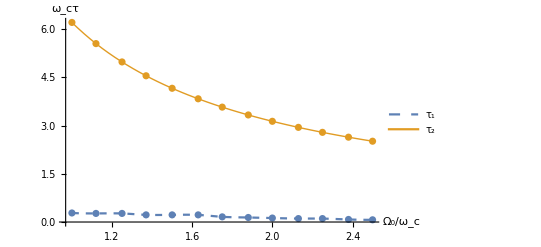

```mathematica
Show[%648,ImageSize->Full]
```